```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX/XS

```mathematica
<<IntegralStuff`
<<PolyLog`
```

```mathematica
XbToX=Get["~/Dropbox/PhD/MathematicaPackages/PolyLog/G012XbToX.m"];
XToXb=Get["~/Dropbox/PhD/MathematicaPackages/PolyLog/G012XToXb.m"];
```

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
LogReRep=Table[
{
ToExpression["Lx1"<>ToString[i]]->Log[1-x1]^i,
ToExpression["Lx2"<>ToString[i]]->Log[1-x2]^i,
ToExpression["Lmx1"<>ToString[i]]->Log[1+x1]^i,
ToExpression["Lmx2"<>ToString[i]]->Log[1+x2]^i
}
,{i,1,5}]//Flatten;
```

```mathematica
powrep={x1^a_ /;a>0:>ToExpression["x1"<>ToString[a]],x2^a_/;a>0:>ToExpression["x2"<>ToString[a]]};
```

## NLO

```mathematica
nr=1;
p1="q";
p2="g";
```

```mathematica
LogRep={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
}
```

{Log[1-x1]^(a_.):>ToExpression[Lx1<>ToString[a]],Log[1-x2]^(a_.):>ToExpression[Lx2<>ToString[a]],Log[1+x1]^(a_.):>ToExpression[Lmx1<>ToString[a]],Log[1+x2]^(a_.):>ToExpression[Lmx2<>ToString[a]]}

```mathematica
(*vars=Table[{Log[1-x1]^i,Log[1+x1]^i,Log[1-x2]^i,Log[1+x2]^i},{i,1,5}]//Flatten;
vars2=vars/.LogRep;
ostr="";
For[i=1,i≤Length[vars],i++,
ostr=ostr<>ToString[CForm[vars2[[i]]]]<>"="<>ToString[CForm[vars[[i]]]]<>";\n";
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["~/Desktop/dump.txt",ostr]*)
```

```mathematica
(*Export["~/Desktop/dump.txt",ToString[InputForm[Variables[Table[{Log[1-x1]^i,Log[1+x1]^i,Log[1-x2]^i,Log[1+x2]^i},{i,1,5}]/.LogRep]]]]*)
```

```mathematica
powrep={x1^a_ :>ToExpression["x1"<>ToString[a]],x2^a_ :>ToExpression["x2"<>ToString[a]]};
```

```mathematica
(*vars=Table[{x1^i,x2^i},{i,2,10}]//Flatten;
vars2=vars/.powrep;
ostr="";
For[i=1,i≤Length[vars],i++,
ostr=ostr<>ToString[CForm[vars2[[i]]]]<>"="<>ToString[CForm[vars[[i]]]]<>";\n";
]
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
Export["~/Desktop/dump.txt",ostr]*)
```

```mathematica
(*Export["~/Desktop/dump.txt",ToString[InputForm[Variables[Table[{x1^i,x2^i},{i,2,10}]/.powrep]]]]*)
```

```mathematica
xs=Expand[Get["Input/xs_NLO_"<>p1<>"_"<>p2<>".m"]/.ALARM->0/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2];
%//Variables
```

{x1,x2,Log[MH2/muf2],Log[1-x1],Log[1+x1],δ[1-x2]}

```mathematica
xs/.x1->z/x2/.z->1-zb/.x2->1-xb
```

-16/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb))/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+16/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb))/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))-(8 (1-xb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb))/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(4 (1-zb))/(3 (1-xb) (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^2)/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^2)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^2)/(3 (1-xb) (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^2)/(3 (1-xb)^2 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3)/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^3)/(3 (1-xb)^3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^4 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4)/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^4)/(3 (1-xb)^4 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(16 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(16 (1-xb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-xb)^2 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-xb)^3 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(16 δ[xb])/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-xb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb)^2 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(8 (1-xb)^3 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(4 (1-xb)^4 δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3 (1-zb))-(8 (1-xb) δ[xb])/(3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3 (1-zb))+(2 (1-zb) δ[xb])/(3 (1-xb))-(8 (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb) δ[xb])/(3 (1-xb) (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-xb) (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-xb)^2 (1-zb) δ[xb])/(3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb) δ[xb])/(3 (1-xb) (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^2 δ[xb])/((-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(8 (1-zb)^2 δ[xb])/(3 (1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(4 (1-zb)^2 δ[xb])/(3 (1-xb)^2 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(8 (1-zb)^3 δ[xb])/(3 (1-xb)^3 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^3 δ[xb])/((1-xb)^2 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^3 δ[xb])/(3 (1-xb)^3 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)+(2 (1-zb)^4 δ[xb])/(3 (1-xb)^4 (-2+xb) (-1+xb-(1-zb)/(1-xb))^3)-(4 (1-zb)^4 δ[xb])/(3 (1-xb)^4 (-2+xb) xb (-1+xb-(1-zb)/(1-xb))^3)-4/3 Log[2] δ[xb]+(4 (1-xb) Log[2] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[2] δ[xb])/(3 (1-xb))-4/3 Log[MH2/muf2] δ[xb]+(4 (1-xb) Log[MH2/muf2] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[MH2/muf2] δ[xb])/(3 (1-xb))-4/3 Log[1-(1-zb)/(1-xb)] δ[xb]+(4 (1-xb) Log[1-(1-zb)/(1-xb)] δ[xb])/(3 (1-zb))+(2 (1-zb) Log[1-(1-zb)/(1-xb)] δ[xb])/(3 (1-xb))+4/3 Log[1+(1-zb)/(1-xb)] δ[xb]-(4 (1-xb) Log[1+(1-zb)/(1-xb)] δ[xb])/(3 (1-zb))-(2 (1-zb) Log[1+(1-zb)/(1-xb)] δ[xb])/(3 (1-xb))

```mathematica
Series[xs/.x2->1-x2b/.δ[x2b]->1,{x2b,0,0}]//Factor
```

1/(3 x1 (1+x1))(6-12 x1+15 x1^2-3 x1^3+4 Log[2]-2 x1^2 Log[2]+2 x1^3 Log[2]+4 Log[MH2/muf2]-2 x1^2 Log[MH2/muf2]+2 x1^3 Log[MH2/muf2]+4 Log[1-x1]-2 x1^2 Log[1-x1]+2 x1^3 Log[1-x1]-4 Log[1+x1]+2 x1^2 Log[1+x1]-2 x1^3 Log[1+x1])+O[x2b]^1

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,1}];
```

```mathematica
xs3=Expand[Collect[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]},_Log,Factor]]//.LogRep//.powrep;
%//Variables
```

{Lmx11,Lx11,x1,x12,x13,x14,x2,x22,x23}

```mathematica
ostr="";
For[i=0,i≤1,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[1]["<>ToString[nr]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NLO/xs_q_g.txt

## NNLO expanded

```mathematica
nr=0;
p1="q";
p2="q";
```

```mathematica
LogRep={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
}
```

{Log[1-x1]^(a_.):>ToExpression[Lx1<>ToString[a]],Log[1-x2]^(a_.):>ToExpression[Lx2<>ToString[a]],Log[1+x1]^(a_.):>ToExpression[Lmx1<>ToString[a]],Log[1+x2]^(a_.):>ToExpression[Lmx2<>ToString[a]]}

```mathematica
powrep={x1^a_ :>ToExpression["x1"<>ToString[a]],x2^a_ :>ToExpression["x2"<>ToString[a]]};
```

```mathematica
xs0=Get["Input/xsexp_NNLO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{nc,ALARM,ALARMδ,δ,Log[MH2/muf2],Log[x1b],Log[x2b],x1b,x2b}

```mathematica
xs=Expand[xs0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.del->δ/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2]/.ALARMδ->0;
xs=Expand[Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}]];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,x1,x2,Log[MH2/muf2],Log[1-x1],Log[1-x2]}

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}];
```

```mathematica
xs3=Expand[Collect[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]},_Log,Factor]]//.LogRep//.powrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,Lx11,Lx12,Lx13,Lx21,Lx22,Lx23,x1,x12,x13,x14,x15,x16,x17,x2,x22,x23,x24,x25,x26,x27}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NNLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NNLO/xs_g_g.txt

## NNLO

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
```

```mathematica
<<HypExp`
```

The package HypExp is already loaded...

$Aborted

```mathematica
$HPLAutoConvertToKnownFunctions=False;
```

### MRRs

```mathematica
UM=Get["~/Dropbox/DDHiggsN3LO/NewVariables/UnmaskerRR.m"];
```

```mathematica
MyIntegrate[a_Plus,b_]:=MyIntegrate[#,b]&/@a;
MyIntegrate[a_List,b_]:=MyIntegrate[#,b]&/@a;
MyIntegrate[a_,b_]:=Integrate[a,b];
JJExp[a___,o_]:=Block[{i,integ,min},
integ=1;
For[i=Length[{a}],i≥1,i--,
integ=SeriesProduct[integ, MySeries[{a}[[i]],x1b,o]/._ALARM->0,x1b,o];
integ=Expand[integ];
integ=MyIntegrate[integ,x1b];
];
Return[integ];
]
JJInt[a___]:=Block[{i,integ},
integ=1;
For[i=Length[{a}],i≥1,i--,
integ=PolyLogInt[integ {a}[[i]],x1b,zz]/.zz->x1b/.G[aa__,αreg]->0;
];
Return[integ];
]
```

```mathematica
MRRs=Cases[{MRR[11,2],MRR[13,1],MRR[14,1],MRR[15,2],MRR[17,2],MRR[20,2],MRR[21,2],MRR[22,2],MRR[28,2],MRR[30,2],MRR[31,2],MRR[33,2],MRRSwap[13,1],MRRSwap[14,1],MRRSwap[15,2],MRRSwap[21,2],MRRSwap[22,2],MRRSwap[28,2]},_MRR];
```

```mathematica
MRRs2=MRRs/.UM;
```

```mathematica
JJs=Select[Cases[Variables[MRRs2],_JJ],FreeQ[#,_sqrt]&]
JJs2=JJs/.JJ[a__]:>JJInt[a];
JJsRep=Table[JJs[[i]]->JJs2[[i]],{i,1,Length[JJs]}];
```

{JJ[1/(1-x1b)],JJ[1/(2-x1b)],JJ[1/x1b],JJ[1/(2-x1b-x2b)],JJ[1/(2-x1b-x2b+x1b x2b)],JJ[1/(1-x1b),1/(1-x1b)],JJ[1/(1-x1b),1/(2-x1b)],JJ[1/(1-x1b),1/x1b],JJ[1/(1-x1b),1/(2-x1b-x2b)],JJ[1/(2-x1b),1/(1-x1b)],JJ[1/(2-x1b),1/(2-x1b)],JJ[1/(2-x1b),1/x1b],JJ[1/(2-x1b),1/(2-x1b-x2b)],JJ[1/x1b,1/(1-x1b)],JJ[1/x1b,1/(2-x1b)],JJ[1/x1b,1/x1b],JJ[1/x1b,1/(2-x1b-x2b)],JJ[1/(2-x1b-x2b),1/(1-x1b)],JJ[1/(2-x1b-x2b),1/(2-x1b)],JJ[1/(2-x1b-x2b),1/x1b],JJ[1/(2-x1b-x2b),1/(2-x1b-x2b)],JJ[1/(2-x1b-x2b+x1b x2b),1/(1-x1b)]}

```mathematica
MRRs3=ShuffleG[MRRs2/.JJsRep,x1b];
```

```mathematica
JJs3=Cases[Variables[MRRs3],_JJ];
JJs4=JJs3/.JJ[a_,b_]/;FreeQ[b,_sqrt]:>GToLog[JJ[a JJInt[b]]]/.Log[-2+a_]->Log[2-a]+I π//.JJ[a_]:>JJ[Expand[a]]//.JJ[a_+b_]->JJ[a]+JJ[b]/.JJ[-a_]->-JJ[a]/.JJ[Log[2-x2b] a_]->Log[2-x2b]JJ[a]/.JJ[Log[2] a_]->Log[2]JJ[a];
JJReps2=Table[JJs3[[i]]->JJs4[[i]],{i,1,Length[JJs3]}];
```

```mathematica
MRRs4=MRRs3//.JJReps2/.Log[2-x2b]->G[2,x2b]+Log[2]//Expand;
```

```mathematica
exp=Cases[Variables[MRRs4[[2;;]]],_JJ]/.sqrt->Sqrt/.JJ[a__]:>JJExp[a,10];
```

```mathematica
exp=Collect[MRRs2[[5]]/.sqrt->Sqrt,_JJ,Factor]/.sqrt->Sqrt/.JJ[a__]:>JJExp[a,10]//PE;
```

### Test Falkos XS

```mathematica
/.-2+a_->-aa(2-a)/.-3+a_->-aa(3-a)/.aa->1/.(-x1b-x2b+x1b x2b)->-aa(x1b+x2b-x1b x2b)/.aa->1/.Log[(x1b-x2b)^2/(2-x1b-x2b)^2]->Log[square[x1b-x2b]]-2 Log[2-x1b-x2b]/.Log[a_]:>PE[Log[a]]
```

```mathematica
xs=Get["Input/xs_NNLO_li_q_Q2.m"]/.Log[MH2]->Log[MH2/muf2]+Log[muf2];
xs=Collect[xs,{_PolyLog,_G,_Log},Factor];
vars=%//Variables
```

{nc,x1b,x2b,Log[MH2/muf2],Log[1-(-1+x1b)^2],Log[1-x1b],Log[1-x1b/2],Log[1-((x1b-x2b) (2+x1b (-1+x2b)-x2b))/(2 (-2+x1b) x1b (-1+x2b))],Log[1-(-1+x2b)^2],Log[1-(-1+x1b)^2 (-1+x2b)^2],Log[1+((x1b-x2b) (2+x1b (-1+x2b)-x2b))/(2 (-1+x1b) (-2+x2b) x2b)],Log[1-x2b/2],Log[1+(x1b x2b)/((-2+x1b) (-2+x2b))],PolyLog[2,(-1+x1b)^2],PolyLog[2,(4 (-1+x1b))/x1b^2],PolyLog[2,(-1+x1b) (-1+x2b)],PolyLog[2,(-1+x1b)^2 (-1+x2b)^2],PolyLog[2,-((-2+x1b) x1b)/((-1+x1b)^2 (-2+x2b) x2b)],PolyLog[2,(x1b (-1+x2b))/x2b],PolyLog[2,(2 (-2+x1b) (-1+x2b))/((x1b (-1+x2b)-x2b) x2b)],PolyLog[2,(2 x1b (-1+x2b))/((2+x1b (-1+x2b)-x2b) x2b)],PolyLog[2,(2 (-1+x1b) x2b)/(x1b (2+x1b (-1+x2b)-x2b))],PolyLog[2,-((-2+x1b) x1b (-1+x2b))/(-2+x1b+x2b)],PolyLog[2,(x1b x2b)/(2 (-2+x1b+x2b))],PolyLog[2,(x1b x2b)/(-2+x1b+x2b)],PolyLog[2,-((-1+x1b) (-2+x2b) x2b)/(-2+x1b+x2b)],PolyLog[2,-(4 (-1+x1b) (-1+x2b))/(x1b+x2b-x1b x2b)^2]}

```mathematica
PLs=Cases[vars,_PolyLog];
PLs2=Expand[Normal[Series[PLs/.x1b->δ x1b/.x2b->δ x2b,{δ,0,5},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1,δ>0,δ<1}]]/.Log[a_]:>PE[Log[Factor[a]]]];
PLsRep=Table[PLs[[i]]->PLs2[[i]],{i,1,Length[PLs]}]/.δ->1;
%//Variables
```

{}

```mathematica
xs2=MySeries[xs/.PLsRep/.x1b->δ x1b/.x2b->δ x2b,δ,3]/.Log[a_]:>PE[Log[Factor[a]]]/.PolyLog[2,-x1b/x2b]->-π^2/6-Log[x1b]^2/2+Log[x1b] Log[x2b]-Log[x2b]^2/2-PolyLog[2,-x2b/x1b]//Expand;
```

```mathematica
xs3=Collector[xs2/.δ->1/._ALARM->0/.Log[muf2]->0/.Log[MH2]->0,{_Log,_PolyLog,_δ},Factor]
```

-1/(384 nc^2)(-1+nc)^2 (1+nc)^2 (-24+8 π^2-72 x1b+8 π^2 x1b-81 x1b^2+16 π^2 x1b^2-101 x1b^3+16 π^2 x1b^3-72 x2b+8 π^2 x2b-216 x1b x2b+8 π^2 x1b x2b-288 x1b^2 x2b+16 π^2 x1b^2 x2b-81 x2b^2+16 π^2 x2b^2-288 x1b x2b^2+16 π^2 x1b x2b^2-101 x2b^3+16 π^2 x2b^3)+((-1+nc)^2 (1+nc)^2 (24+12 x1b+21 x1b^2+38 x1b^3+12 x2b+12 x1b x2b+3 x1b^2 x2b+21 x2b^2+3 x1b x2b^2+38 x2b^3) Log[x1b])/(192 nc^2)+((-1+nc)^2 (1+nc)^2 (1+x1b+2 x1b^2+2 x1b^3+x2b+x1b x2b+2 x1b^2 x2b+2 x2b^2+2 x1b x2b^2+2 x2b^3) Log[x1b]^2)/(16 nc^2)+((-1+nc)^2 (1+nc)^2 (24+12 x1b+21 x1b^2+38 x1b^3+12 x2b+12 x1b x2b+3 x1b^2 x2b+21 x2b^2+3 x1b x2b^2+38 x2b^3) Log[x2b])/(192 nc^2)+((-1+nc)^2 (1+nc)^2 (1+x1b+2 x1b^2+2 x1b^3+x2b+x1b x2b+2 x1b^2 x2b+2 x2b^2+2 x1b x2b^2+2 x2b^3) Log[x1b] Log[x2b])/(8 nc^2)+((-1+nc)^2 (1+nc)^2 (1+x1b+2 x1b^2+2 x1b^3+x2b+x1b x2b+2 x1b^2 x2b+2 x2b^2+2 x1b x2b^2+2 x2b^3) Log[x2b]^2)/(16 nc^2)

```mathematica
xs=MySeries[Coefficient[Get["Input/xsexp_NNLO_q_Q2.m"]/.Log[MH2]->Log[MH2/muf2]+Log[muf2],Log[x2b],2],δ,3]/._ALARM->0/.δ->1//Factor
```

((-1+nc)^2 (1+nc)^2 (1+x1b+2 x1b^2+2 x1b^3+x2b+x1b x2b+2 x1b^2 x2b+2 x2b^2+2 x1b x2b^2+2 x2b^3))/(16 nc^2)

### Collect dummy variables

```mathematica
<<PolyLog`
```

```mathematica
xss={Get["Input/xs_NNLO_li_g_g.m"],Get["Input/xs_NNLO_li_q_g.m"],Get["Input/xs_NNLO_li_g_q.m"],Get["Input/xs_NNLO_li_q_qbar.m"],Get["Input/xs_NNLO_li_q_q.m"],Get["Input/xs_NNLO_li_q_Q2.m"]};
```

```mathematica
Get["Input/xs_NNLO_li_q_Q2.m"]/.x1b->0.1/.x2b->0.01/.nc->3//Expand
Get["Input/xs_NNLO_q_Q2.m"]/.x1b->0.1/.x2b->0.01/.nc->3//.GLogExtract/.G2Log/.GExpand[10]//Expand
Get["Input/xsexp_NNLO_q_Q2.m"]/.x1b->0.1/.x2b->0.01/.nc->3//.GLogExtract/.G2Log/.GExpand[10]/.δ->1/.ALARM->0/. ALARMδ->0//Expand
```

16.4514-6.0133 Log[MH2/muf2]+0.503854 Log[MH2/muf2]^2

16.4514-6.0133 Log[MH2/muf2]+0.503854 Log[MH2/muf2]^2

16.4514-6.0133 Log[MH2/muf2]+0.503854 Log[MH2/muf2]^2

```mathematica
xss2=xss/.Log[a_]:>Log[PE[Factor[a]]]/.-2+a_->-aa(2-a)/.-3+a_->-aa(3-a)/.aa->1/.(-x1b-x2b+x1b x2b)->-aa(x1b+x2b-x1b x2b)/.aa->1/.Log[(x1b-x2b)^2/(2-x1b-x2b)^2]->Log[square[x1b-x2b]]-2 Log[2-x1b-x2b]/.Log[a_]:>PE[Log[a]]/.Log[a_]:>Log[a/.x1b->1-x1/.x2b->1-x2]/.LogRep2;
```

```mathematica
PolyLogs=Cases[Variables[xss2],_PolyLog];
GNNLORep=Table[PolyLogs[[i]]->ToExpression["GNNLO"<>ToString[i]],{i,1,Length[PolyLogs]}];
```

```mathematica
Logs=DeleteCases[DeleteCases[Cases[Variables[xss2],_Log],Log[MH2]],Log[muf2]]
LogNNLORep=Table[Logs[[i]]->ToExpression["LogNNLO"<>ToString[i]],{i,1,Length[Logs]}];
```

{Log[3-2 (1-x1)],Log[x1],Log[3-2 (1-x2)],Log[2-x1-(1-x1) (1-x2)-x2],Log[x2],Log[x1+x2],Log[x1+(1-x1) (1-x2)+x2],Log[square[-x1+x2]]}

```mathematica
MRRs={Cases[Variables[xss2],_MRR],Cases[Variables[xss2],_MRRSwap]}//Flatten
MRRNNLORep=Table[MRRs[[i]]->ToExpression["MRRNNLO"<>ToString[i]],{i,1,Length[MRRs]}];
```

{MRR[11,2],MRR[13,1],MRR[14,1],MRR[15,2],MRR[17,2],MRR[20,2],MRR[21,2],MRR[22,2],MRR[28,2],MRR[30,2],MRR[31,2],MRR[33,2],MRRSwap[13,1],MRRSwap[14,1],MRRSwap[15,2],MRRSwap[21,2],MRRSwap[22,2],MRRSwap[28,2]}

```mathematica
xss3=xss2/.GNNLORep/.LogNNLORep/.MRRNNLORep;
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO13,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO24,GNNLO25,GNNLO26,GNNLO27,GNNLO28,GNNLO29,GNNLO3,GNNLO30,GNNLO31,GNNLO32,GNNLO33,GNNLO34,GNNLO35,GNNLO36,GNNLO37,GNNLO38,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO6,GNNLO7,GNNLO8,GNNLO9,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO3,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,LogNNLO8,Lx11,Lx21,MRRNNLO1,MRRNNLO10,MRRNNLO11,MRRNNLO12,MRRNNLO13,MRRNNLO14,MRRNNLO15,MRRNNLO16,MRRNNLO17,MRRNNLO18,MRRNNLO2,MRRNNLO3,MRRNNLO4,MRRNNLO5,MRRNNLO6,MRRNNLO7,MRRNNLO8,MRRNNLO9,nc,nf,x1b,x2b,Log[MH2],Log[muf2],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
Export["~/Desktop/dump.txt",ToString[MRRNNLORep[[;;,2]]]]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[LogNNLORep],i++,
ostr=ostr<>ToString[LogNNLORep[[i,2]]]<>"="<>ToString[CForm[LogNNLORep[[i,1]]/.Log[a_]:>Log[Expand[a]]/.square[a_]->a^2]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[GNNLORep],i++,
ostr=ostr<>ToString[GNNLORep[[i,2]]]<>"="<>ToString[CForm[GNNLORep[[i,1]]/.x1b->1-x1/.x2b->1-x2/.PolyLog[2,a_]->HPL[0,1,a]/.PolyLog[3,a_]->HPL[0,0,1,a]//N]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[0]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
UM=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/Unmasker_Expanded20.m"];
```

```mathematica
{x1b,x2b}/.x1b->1-x1/.x2b->1-x2/.x2->x/.x1->z/x/.x->1-xb/.z->1-zb/.xb->xb zb//Factor
%/.xb->1/10//Factor
```

{((-1+xb) zb)/(-1+xb zb),xb zb}

{-(9 zb)/(-10+zb),zb/10}

```mathematica
solback=Solve[{x1b==((-1+xb) zb)/(-1+xb zb),x2b==xb zb},{xb,zb}][[1]]/.{x1b->x2b,x2b->x1b}/.x1b->1-x1/.x2b->1-x2//Factor
```

{xb→(-1+x1)/(-1+x1 x2),zb→1-x1 x2}

```mathematica
UM2=MySeries[UM/.x1b->((-1+xb) zb)/(-1+xb zb)/.x2b->xb zb/.Log[a_]:>PE[Log[PE[a]]],zb,20];
```

```mathematica
MRNNLO2=Expand[MRRNNLORep[[;;,1]]/.MRR[a_,b_]:>Coefficient[UM2[[a]],ϵ,b]/.MRRSwap[a_,b_]:>(Coefficient[UM2[[a]],ϵ,b]/.{x1b->x2b,x2b->x1b})/.δ->1/.x1b->1-x1/.x2b->1-x2/.LogRep2];
%//Variables//Sort
```

{xb,zb,Log[1-xb],Log[xb],Log[zb]}

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[N[MRNNLO2[[i]],17]]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

### Create XS

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=6;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=xss3[[nr]]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.PlusD[a_,b_]->Log[a]^b (1-δ[a])/a/.nc->3/.nf->5;
vars=%//Variables
```

{GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO27,GNNLO4,GNNLO5,GNNLO6,Lmx11,Lmx21,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx21,x1b,x2b,Log[MH2/muf2]}

```mathematica
(*{x1,x2}/.x1->z/x2/.x2->1-xb/.xb ->(1-z)xb/.z->1-zb
trafo=Solve[{x1==%[[1]],x2==%[[2]]},{zb,xb}][[1]]
Jac=Det[{{D[zb/.trafo,x1],D[xb/.trafo,x1]},{D[zb/.trafo,x2],D[xb/.trafo,x2]}}]//Factor;
xs0=Coefficient[Jac Get["~/Dropbox/HiggsCrossSection/LowerOrder/Results/qQ2NNLO.m"][[1]]/.Nc->3/.nf->5/.ALARM->0/.zb->1-z/.z->x1 x2,ϵ,0];
%//Variables*)
```

```mathematica
xs=Collector[xs0,Complement[vars,{nc,x1b,x2b}],Factor]/.δ[x1b]δ[x2b]->δ[x1b,x2b];
```

```mathematica
myxs=Get["Input/xs_NNLO_q_Q2.m"];
Gs=Cases[%//Variables,_G];
Gs2=MySeries[Gs//.GLogExtract/.G2Log/.GExpand[10]/.x1b->δ x1b/.x2b->δ x2b,δ,8]/.δ->1/._ALARM->0//Expand;
GsRep=Table[Gs[[i]]->Gs2[[i]],{i,1,Length[Gs]}];
myxs=MySeries[myxs/.GsRep/.x1b->δ x1b/.x2b->δ x2b/.Log[a_ δ]->Log[a],δ,6]/.nc->3/.nf->5/.δ->1//Expand;
myxs=Expand[myxs/.x1b->1-x1/.x2b->1-x2]/.LogRep2/.powrep/._ALARM->0;
xs=myxs;
```

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2}/.LogRep2;
```

```mathematica
xs3={xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]};
vars2=%//Variables
```

{Lx11,Lx12,Lx21,Lx22,x1,x12,x13,x14,x15,x16,x2,x22,x23,x24,x25,x26}

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc}],Factor]/.powrep/.G2HPL/.ϵ->0/.HPL[{a___},b_]->HPL[a,b]/.Log->log;
%//Variables
```

{Lx11,Lx12,Lx21,Lx22,x1,x12,x13,x14,x15,x16,x2,x22,x23,x24,x25,x26}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow"}];
```

```mathematica
Export["NNLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NNLO/xs_q_Q2.txt

## NNLO Numerical

```mathematica
LogRep2={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
};
LogReRep=Table[
{
ToExpression["Lx1"<>ToString[i]]->Log[1-x1]^i,
ToExpression["Lx2"<>ToString[i]]->Log[1-x2]^i,
ToExpression["Lmx1"<>ToString[i]]->Log[1+x1]^i,
ToExpression["Lmx2"<>ToString[i]]->Log[1+x2]^i
}
,{i,1,5}]//Flatten;
```

```mathematica
<<HypExp`
```

The package HypExp is already loaded...

$Aborted

```mathematica
$HPLAutoConvertToKnownFunctions=False;
```

```mathematica
powrep={x1^a_ /;a>0:>ToExpression["x1"<>ToString[a]],x2^a_/;a>0:>ToExpression["x2"<>ToString[a]]};
```

### Collect dummy variables

```mathematica
<<PolyLog`
```

```mathematica
xss={Get["Input/xs_NNLO_li_g_g.m"],Get["Input/xs_NNLO_li_q_g.m"],Get["Input/xs_NNLO_li_g_q.m"],Get["Input/xs_NNLO_li_q_qbar.m"],Get["Input/xs_NNLO_li_q_q.m"],Get["Input/xs_NNLO_li_q_Q2.m"]};
```

```mathematica
xss2=xss/.Log[a_]:>Log[PE[Factor[a]]]/.-2+a_->-aa(2-a)/.-3+a_->-aa(3-a)/.aa->1/.(-x1b-x2b+x1b x2b)->-aa(x1b+x2b-x1b x2b)/.aa->1/.Log[(x1b-x2b)^2/(2-x1b-x2b)^2]->Log[square[x1b-x2b]]-2 Log[2-x1b-x2b]/.Log[a_]:>PE[Log[a]]/.Log[a_]:>Log[a/.x1b->1-x1/.x2b->1-x2]/.LogRep2;
```

```mathematica
Cases[Get["Input/xs_NNLO_li_q_qbar.m"]//Variables,_MRR]
```

{MRR[13,1],MRR[14,1],MRR[22,2],MRR[28,2]}

```mathematica
PolyLogs=Cases[Variables[xss2],_PolyLog];
GNNLORep=Table[PolyLogs[[i]]->ToExpression["GNNLO"<>ToString[i]],{i,1,Length[PolyLogs]}];
```

```mathematica
Logs=DeleteCases[DeleteCases[Cases[Variables[xss2],_Log],Log[MH2]],Log[muf2]]
LogNNLORep=Table[Logs[[i]]->ToExpression["LogNNLO"<>ToString[i]],{i,1,Length[Logs]}];
```

{Log[3-2 (1-x1)],Log[x1],Log[3-2 (1-x2)],Log[2-x1-(1-x1) (1-x2)-x2],Log[x2],Log[x1+x2],Log[x1+(1-x1) (1-x2)+x2],Log[square[-x1+x2]]}

```mathematica
MRRs={Cases[Variables[xss2],_MRR],Cases[Variables[xss2],_MRRSwap]}//Flatten
MRRNNLORep=Table[MRRs[[i]]->ToExpression["MRRNNLO"<>ToString[i]],{i,1,Length[MRRs]}];
```

{MRR[11,2],MRR[13,1],MRR[14,1],MRR[15,2],MRR[17,2],MRR[20,2],MRR[21,2],MRR[22,2],MRR[28,2],MRR[30,2],MRR[31,2],MRR[33,2],MRRSwap[13,1],MRRSwap[14,1],MRRSwap[15,2],MRRSwap[21,2],MRRSwap[22,2],MRRSwap[28,2]}

```mathematica
xss3=xss2/.GNNLORep/.LogNNLORep/.MRRNNLORep;
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO13,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO24,GNNLO25,GNNLO26,GNNLO27,GNNLO28,GNNLO29,GNNLO3,GNNLO30,GNNLO31,GNNLO32,GNNLO33,GNNLO34,GNNLO35,GNNLO36,GNNLO37,GNNLO38,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO6,GNNLO7,GNNLO8,GNNLO9,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO3,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,LogNNLO8,Lx11,Lx21,MRRNNLO1,MRRNNLO10,MRRNNLO11,MRRNNLO12,MRRNNLO13,MRRNNLO14,MRRNNLO15,MRRNNLO16,MRRNNLO17,MRRNNLO18,MRRNNLO2,MRRNNLO3,MRRNNLO4,MRRNNLO5,MRRNNLO6,MRRNNLO7,MRRNNLO8,MRRNNLO9,nc,nf,x1b,x2b,Log[MH2],Log[muf2],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
xss4=Expand[xss3-(xss3/._PlusD->0/._δ->0)];
```

```mathematica
xss5=Expand[xss3-xss4];
```

$Aborted

```mathematica
Export["~/Desktop/dump.txt",ToString[MRRNNLORep[[;;,2]]]]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[LogNNLORep],i++,
ostr=ostr<>ToString[LogNNLORep[[i,2]]]<>"="<>ToString[CForm[LogNNLORep[[i,1]]/.Log[a_]:>Log[Expand[a]]/.square[a_]->a^2]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[GNNLORep],i++,
ostr=ostr<>ToString[GNNLORep[[i,2]]]<>"="<>ToString[CForm[GNNLORep[[i,1]]/.x1b->1-x1/.x2b->1-x2/.PolyLog[2,a_]->HPL[0,1,a]/.PolyLog[3,a_]->HPL[0,0,1,a]//N]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[0]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

```mathematica
UM=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/Unmasker_Expanded20.m"];
```

```mathematica
MRNNLO2=Expand[MRRNNLORep[[;;,1]]/.MRR[a_,b_]:>Coefficient[UM2[[a]],ϵ,b]/.MRRSwap[a_,b_]:>(Coefficient[UM2[[a]],ϵ,b]/.{x1b->x2b,x2b->x1b})/.δ->1/.x1b->1-x1/.x2b->1-x2/.LogRep2];
%//Variables//Sort
```

Part::partd: Part specification UM2⟦11⟧ is longer than depth of object.

Part::partd: Part specification UM2⟦13⟧ is longer than depth of object.

Part::partd: Part specification UM2⟦14⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
ostr="";
For[i=1,i≤Length[MRRNNLORep],i++,
ostr=ostr<>ToString[MRRNNLORep[[i,2]]]<>"="<>ToString[CForm[N[MRNNLO2[[i]],17]]]<>";\n"
]
ostr=StringReplace[ostr,{"Log"->"log","Power"->"pow"}];
Export["~/Desktop/dump.txt",ostr]
```

~/Desktop/dump.txt

### Create XS

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=3;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=xss4[[nr]]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.PlusD[a_,b_]->Log[a]^b (1-δ[a])/a/.nc->3/.nf->5;
vars=%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx21,x1b,x2b,Log[MH2/muf2],Log[muf2],Log[x1b],δ[x1b]}

```mathematica
xs=Collector[xs0,Complement[vars,{nc,x1b,x2b}],Factor]/.δ[x1b]δ[x2b]->δ[x1b,x2b];
```

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.{x1b->1-x1,x2b->1-x2}/.LogRep2;
```

```mathematica
xs3={xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]};
vars2=%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx12,Lx21,x1,x2}

```mathematica
1/x1 /.powrep
```

1/x1

```mathematica
xs4=Collector[xs3,Complement[vars2,{x1,x2,nc}],Factor]/.powrep;
%//Variables
```

{GNNLO1,GNNLO10,GNNLO11,GNNLO12,GNNLO14,GNNLO15,GNNLO16,GNNLO17,GNNLO18,GNNLO19,GNNLO2,GNNLO20,GNNLO21,GNNLO22,GNNLO23,GNNLO25,GNNLO26,GNNLO27,GNNLO3,GNNLO39,GNNLO4,GNNLO40,GNNLO41,GNNLO42,GNNLO43,GNNLO44,GNNLO45,GNNLO46,GNNLO47,GNNLO48,GNNLO49,GNNLO5,GNNLO7,GNNLO8,Lmx11,Lmx21,LogNNLO1,LogNNLO2,LogNNLO4,LogNNLO5,LogNNLO6,LogNNLO7,Lx11,Lx12,Lx21,x1,x2,x22,x23}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs4[[j+1,i+1]],0]&&!MatchQ[j,0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs4[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow"}];
```

```mathematica
Export["NumericalNNLO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NumericalNNLO/xs_g_q.txt

### Create XS - Numerical Part

```mathematica
RRes=Table[StringReplace[Import["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/Results/Result"<>ToString[i]<>".txt"],{"e-"->"*10^-",",}"->"}"}]//ToExpression,{i,0,55}];
```

```mathematica
GetBin[x_]:=If[x<0.99,Return[Floor[x 100]],Return[Floor[99+(x-0.99)*2000]]]
GetRes[a_,x1_,x2_]:=RRes[[a+1,GetBin[x1]119+GetBin[x2]+1,3]];
GetRes[1,0.992,0.999]
```

0.00350422

```mathematica
G2Rep=G[a_,b_,tt_]/;!MatchQ[a,b]&&!MatchQ[a,0]:>(-Log[-a] Log[-b/(a-b)]+Log[-a] (Log[b]-Log[b-y])+Log[-a+y] Log[(-b+y)/(a-b)]-PolyLog[2,a/(a-b)]+PolyLog[2,(a-y)/(a-b)]/.y->tt);
```

```mathematica
stupidGs={G[3/2,1,x1b],G[3/2,1,x2b],G[3/2,2,x1b],G[3/2,2,x2b]};
stupidGs2={
π^2/6+Log[2]^2/2+Log[3-2 x1b] Log[1-x1b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x1b)],
π^2/6+Log[2]^2/2+Log[3-2 x2b] Log[1-x2b]+PolyLog[2,-1/2]+PolyLog[2,2 (-1+x2b)],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x1b]) Log[1-x1b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x1b],
-π^2/3+2 ⅈ π Log[2]+2 Log[2]^2+(ⅈ π+Log[3-2 x2b]) Log[1-x2b/2]+PolyLog[2,1/4]+PolyLog[2,4-2 x2b]
};
%/.x1b->0.3/.x2b->0.1//Re
SGRep=Table[stupidGs[[i]]->stupidGs2[[i]],{i,1,Length[stupidGs]}];
stupidGs/.G[a__]:>GNIntegrate[G[a],{x1b->3/10,x2b->1/10}]
```

{0.0389106,0.00361254,0.0183156,0.00177466}

{0.0389106,0.00361254,0.0183156,0.00177466}

```mathematica
MRRRep=Get["~/Dropbox/Projects/HiggsRap/NNLO/5-point/MasterCalc/NumericalDiffEqs/MRRRep.m"]/.M[a_]->Res[a,x1b,x2b]//.GLogExtract/.G2Log/.SGRep;
%[[;;,2]]//Variables
MRRRepSwap=MRRRep/.{x1b->x2b,x2b->x1b}/.MRR->MRRSwap;
```

{x1b,x2b,G[2,x1b],G[2,x2b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[1,2,x1b],G[1,2,x2b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],Log[3-2 x1b],Log[1-x1b],Log[1-x1b/2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[1-x2b/2],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[22,x1b,x2b],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[31,x1b,x2b],Res[33,x1b,x2b],Res[34,x1b,x2b],Res[36,x1b,x2b],Res[37,x1b,x2b],Res[39,x1b,x2b],Res[40,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b],Res[48,x1b,x2b],Res[49,x1b,x2b],Res[51,x1b,x2b],Res[52,x1b,x2b],Res[54,x1b,x2b],Res[55,x1b,x2b]}

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=4;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=Get["~/Dropbox/DDHiggsN3LO/NewVariables/FiniteXS/xs_NNLO_"<>p1<>"_"<>p2<>".m"]/.PlusD[a_,b_]->0/.nc->3/.nf->5/.δ[a_]->0/.del[a_]->0/.MRRRep/.MRRRepSwap//.SGRep/.GLogExtract/.G2Log/.Log[a_]:>Log[Factor[a]];
vars=%//Variables
```

{x1b,x2b,G[2,x1b],G[2,x2b],G[2-x2b,x1b],G[-(2-x2b)/(-1+x2b),x1b],G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[0,-(2-x2b)/(-1+x2b),x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2,x1b],G[2,2,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[2-x2b,2-x2b,x1b],G[-(2-x2b)/(-1+x2b),1,x1b],G[-(2-x2b)/(-1+x2b),2,x1b],G[-(2-x2b)/(-1+x2b),2-x2b,x1b],Log[MH2/muf2],Log[3-2 x1b],Log[1-x1b],Log[(2-x1b)/2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[(2-x2b)/2],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,x1b,x2b],Res[28,x1b,x2b],Res[42,x1b,x2b],Res[43,x1b,x2b],Res[45,x1b,x2b],Res[46,x1b,x2b]}

```mathematica
point={x1b->0.1,x2b->0.4};
```

```mathematica
GRep=RewriteGs[Complement[Select[Cases[vars,_G],!FreeQ[#,x1b]&&!FreeQ[#,x2b]&],{G[x2b,2,x1b],G[x2b,x1b],G[x2b/x1b,1]}],x2b,point];
```

```mathematica
GRep2=RewriteGs[Complement[Select[Cases[vars,_G],!FreeQ[#,x1b]&&!FreeQ[#,x2b]&],{G[x1b,2,x2b],G[x1b,x2b],G[x2b/x1b,1]}],x1b,point];
```

```mathematica
GExp1=G[x2b,2,x1b]->Normal[Series[G[x2b,2,x1b]/.GReps,{x2b,0,1},Assumptions->{x2b>0,x2b<1,x1b<1,x1b>0}]];
GExp1={GExp1,GExp1/.{x1b->x2b,x2b->x1b}}//Flatten;
```

```mathematica
xsexp=Normal[Series[xs0//.GLogExtract/.G2Log//.GRep2//.GExp1//.GLogExtract/.G2Log/.G[a__,x1b]:>(G[a,x1b]/.GExpand[4])//GToLog,{x1b,0,0},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]]/.Derivative[0,0,1][Res][a_,b_,c_]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0;
%//Variables
```

{x2b,G[0,1,x2b],G[0,2,x2b],G[1,2,x2b],G[2,1,x2b],Log[MH2/muf2],Log[x1b],Log[3-2 x2b],Log[1-x2b],Log[(2-x2b)/2],Log[2-x2b],Log[x2b],PolyLog[2,4-2 x2b],PolyLog[2,2 (-1+x2b)],Res[26,0,x2b],Res[28,0,x2b],Res[42,0,x2b],Res[43,0,x2b],Res[45,0,x2b],Res[46,0,x2b]}

```mathematica
xsexp02=Normal[Series[xs0/.GExp1/.GRep//.GLogExtract/.G2Log/.G[a__,x2b]:>(G[a,x2b]/.GExpand[6])//GToLog,{x2b,0,0},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]]/.Derivative[0,0,1][Res][a_,b_,c_]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0;
%//Variables
```

{x1b,G[0,1,x1b],G[0,2,x1b],G[1,2,x1b],G[2,1,x1b],Log[MH2/muf2],Log[1-2/x1b],Log[3-2 x1b],Log[1-x1b],Log[(2-x1b)/2],Log[2-x1b],Log[-2/x1b],Log[x1b],Log[x2b],PolyLog[2,4-2 x1b],PolyLog[2,2 (-1+x1b)],Res[26,x1b,0],Res[28,x1b,0],Res[42,x1b,0],Res[43,x1b,0],Res[45,x1b,0],Res[46,x1b,0]}

```mathematica
zerolim={Res[28,0,x2b]->0,Res[31,0,x2b]->0,Res[39,0,x2b]->0,Res[40,0,x2b]->0,Res[43,0,x2b]->0,Res[42,0,x2b]->0,Res[39,x1b,0]->-Res[42,x1b,0],Res[46,0,0]->0,Res[45,0,0]->0,Res[26,0,0]->0,Res[43,0,0]->-Res[40,0,0],
Res[31,x1b,0]->(Log[2] Log[1-x1b])/(128 π^3 x1b)-(9 (5-4 x1b+x1b^2) Log[1-x1b]^2)/(1024 π^3 x1b (1+x1b^2))-(ⅈ (4 π-9 ⅈ Log[2]) Log[2-x1b])/(512 π^3 x1b)+((41-36 x1b+5 x1b^2) Log[1-x1b] Log[2-x1b])/(256 π^3 x1b (1+x1b^2))-(9 Log[2] Log[x1b])/(512 π^3 x1b)+(9 Log[2-x1b] Log[x1b])/(512 π^3 x1b)-(217 π^2-252 π^2 x1b+97 π^2 x1b^2-1188 ⅈ π Log[2]+1296 ⅈ π x1b Log[2]-420 ⅈ π x1b^2 Log[2]-108 Log[2]^2-108 x1b^2 Log[2]^2-1188 PolyLog[2,2]+1296 x1b PolyLog[2,2]-420 x1b^2 PolyLog[2,2])/(6144 π^3 x1b (-ⅈ+x1b) (ⅈ+x1b))+(9 PolyLog[2,(2-x1b)/2])/(512 π^3 x1b)-PolyLog[2,2-x1b]/(128 π^3 x1b)+((43-36 x1b+7 x1b^2) PolyLog[2,-1+x1b])/(256 π^3 x1b (1+x1b^2))+(9 PolyLog[2,x1b/2])/(512 π^3 x1b)+(9 (5-4 x1b+x1b^2) Res[40,x1b,0])/(8 x1b (1+x1b^2))+(9 (5-4 x1b+x1b^2) Res[43,x1b,0])/(8 x1b (1+x1b^2)),
Res[34,0,0]->0,Res[33,0,0]->0,Res[22,0,0]->0,Res[51,0,0]->0,Res[54,0,0]->0,Res[52,0,0]->- Res[55,0,0],Res[33,0,x2b]->-Res[45,0,x2b],
Res[46,0,x2b]->((-2+x2b) (1-x2b+x2b^2)^2 G[1,2,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)+((-2+23 x2b-44 x2b^2+37 x2b^3-16 x2b^4+3 x2b^5) G[2,1,x2b])/(64 π^3 x2b (3-3 x2b+x2b^2)^2)-Log[1-x2b]^2/(128 π^3)+(2 (-2+x2b) (1-x2b+x2b^2)^2 Res[22,0,x2b])/((3-3 x2b+x2b^2)^2)-Res[34,0,x2b],Res[39,x2b,0]->-Res[42,x2b,0],
Res[43,x2b,0]->((1+x2b^2) G[1,2,x2b])/(144 π^3 (5-4 x2b+x2b^2))-((43-36 x2b+7 x2b^2) G[2,1,x2b])/(288 π^3 (5-4 x2b+x2b^2))+Log[1-x2b]^2/(128 π^3)+(8 x2b (1+x2b^2) Res[31,x2b,0])/(9 (5-4 x2b+x2b^2))-Res[40,x2b,0],
G[0,2,x2b]->1/6 (-π^2+6 Log[2]^2-6 Log[2] Log[2-x2b]-6 Log[2] Log[x2b]+6 Log[2-x2b] Log[x2b]+6 PolyLog[2,(2-x2b)/2]),
Res[43,0,0]->0,Res[42,0,0]->0,Res[28,0,0]->0,Res[31,0,0]->0,Res[40,0,0]->0};
%/.x2b->0.5/.x1b->0.5/.Res->GetRes/.GExpand[40]
```

{1.67571×10^-15→0,-2.6723×10^-15→0,-3.35954×10^-15→0,-6.25772×10^-15→0,3.13317×10^-15→0,3.35954×10^-15→0,-0.000210892→-0.000210892,-6.23894×10^-15→0,-3.14956×10^-15→0,1.26258×10^-15→0,6.14802×10^-15→6.14802×10^-15,-0.000100487→-0.000100487-1.0842×10^-19 ⅈ,6.23894×10^-15→0,3.14956×10^-15→0,-1.25982×10^-15→0,3.14956×10^-15→0,-3.14956×10^-15→0,0.000621699→0.000621699,0.000210892→0.000210892,-0.000230821→-0.000230821,-0.000210892→-0.000210892,0.000230821→0.000230821,-0.267653→-0.267653,6.14802×10^-15→0,3.14956×10^-15→0,1.26244×10^-15→0,-1.25982×10^-15→0,-6.14802×10^-15→0}

```mathematica
xsexp1=Collector[ShuffleG[ShuffleG[Expand[xsexp]//.zerolim,x2b],x1b]/.Log[MH2]->Log[MH2/muf2]+Log[muf2],{_G,_Log,_Res},Factor];
xsexp2=Coefficient[Collector[ShuffleG[ShuffleG[Expand[xsexp02],x2b],x1b]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]//.zerolim,{_G,_Log,_Res},Factor]/.Derivative[0,0,1][Res][a_,x1b,0]->0/.Derivative[0,1,0][Res][a_,b_,c_]->0,x2b,0];
xsexp12=MySeries[xsexp1/.GLogExtract/.G2Log/.GExpand[5],x2b,0]/.zerolim/._ALARM->0
```

-4/27 (-3+π^2)+8/9 Log[MH2/muf2]+4/9 Log[MH2/muf2]^2+(8 Log[x1b])/9+8/9 Log[MH2/muf2] Log[x1b]+(4 Log[x1b]^2)/9+(8 Log[x2b])/9+8/9 Log[MH2/muf2] Log[x2b]+8/9 Log[x1b] Log[x2b]+(4 Log[x2b]^2)/9

```mathematica
MySeries[xsexp1//.GLogExtract/.G2Log//GToLog,x1b,-1]/._ALARM->0//Factor
%/.x2b->0.5/.Res->GetRes//.GExpand[40]
Collect[%%,{_G,_Res},Factor]
Collect[Solve[%==0,Res[43,x2b,0]],{_G,_Res},Factor]
```

0

0

0

{{}}

```mathematica
xs=Collector[xs0+lim1 xsexp1+lim2 xsexp2+lim12 xsexp12,Complement[Variables[xs0+lim1 xsexp1+lim2 xsexp2+lim12 xsexp12],{nc,x1b,x2b}],Factor]/.δ[x1b]δ[x2b]->δ[x1b,x2b];
```

```mathematica
xs2=(Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]//.GLogExtract//GToLog)/.Log[-2+a_]->Log[2-a]+I π;
%//Variables
```

{lim1,lim12,lim2,x1b,x2b,G[0,1,x1b],G[0,1,x2b],G[0,2,x1b],G[0,2,x2b],G[0,2-x2b,x1b],G[0,-(2-x2b)/(-1+x2b),x1b],G[1,2,x1b],G[1,2,x2b],G[1,2-x2b,x1b],G[2,1,x1b],G[2,1,x2b],G[2,2-x2b,x1b],G[2-x2b,1,x1b],G[2-x2b,2,x1b],G[-(2-x2b)/(-1+x2b),1,x1b],G[-(2-x2b)/(-1+x2b),2,x1b],G[-(2-x2b)/(-1+x2b),2-x2b,x1b],Log[1-x1b],Log[2-x1b],Log[x1b],Log[x1b+(2-x2b)/(-1+x2b)],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[(2-x2b)/(-1+x2b)],Log[x2b],PolyLog[2,(2-x2b)/2],Res[22,0,x2b],Res[26,0,x2b],Res[26,x1b,0],Res[26,x1b,x2b],Res[28,x1b,0],Res[28,x1b,x2b],Res[34,0,x2b],Res[42,x1b,0],Res[42,x1b,x2b],Res[43,x1b,0],Res[43,x1b,x2b],Res[45,0,x2b],Res[45,x1b,0],Res[45,x1b,x2b],Res[46,x1b,0],Res[46,x1b,x2b]}

```mathematica
terms=List@@Expand[Normal[Series[x1b^(-ϵ)x2b^(-ϵ),{ϵ,0,5}]]]/.ϵ->1;
LogPows=Table[{Exponent[terms[[i]],Log[x1b]],Exponent[terms[[i]],Log[x2b]]},{i,1,Length[terms]}]
%//Length
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{0,1},{1,1},{2,1},{3,1},{4,1},{0,2},{1,2},{2,2},{3,2},{0,3},{1,3},{2,3},{0,4},{1,4},{0,5}}

21

```mathematica
GReps={
G[1,2,x1b]->-π^2/4-Log[2] Log[1-x1b]+ⅈ π Log[2-x1b]+Log[1-x1b] Log[2-x1b]+PolyLog[2,2-x1b],
G[1,2,x2b]->-π^2/4+ⅈ π Log[2-x2b]-Log[1-x2b] Log[-2/(-2+x2b)]+PolyLog[2,2-x2b],
G[1,2-x2b,x1b]->ⅈ π Log[1+x1b/(-2+x2b)]+Log[1+x1b/(-2+x2b)] Log[(-1+x1b)/(-1+x2b)]-PolyLog[2,(-2+x2b)/(-1+x2b)]+PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],
G[2,1,x1b]->π^2/12+Log[1-x1b] Log[2-x1b]+PolyLog[2,-1+x1b],
G[2,1,x2b]->π^2/12+Log[1-x2b] Log[2-x2b]+PolyLog[2,-1+x2b],
G[2,2-x2b,x1b]->ⅈ π Log[2]-ⅈ π Log[2-x1b]+Log[2] Log[2-x2b]-Log[2-x1b] Log[2-x2b]-Log[2] Log[x2b]+Log[2-x1b] Log[x2b]+PolyLog[2,2/x2b]-PolyLog[2,(2-x1b)/x2b],
G[2-x2b,1,x1b]->Log[1-x1b] Log[(-2+x1b+x2b)/(-1+x2b)]-PolyLog[2,1/(-1+x2b)]+PolyLog[2,(1-x1b)/(-1+x2b)],
G[2-x2b,2,x1b]->-ⅈ π Log[2]+ⅈ π Log[2-x1b]+Log[2] Log[-x2b/(-2+x1b+x2b)]-Log[2-x1b] Log[-x2b/(-2+x1b+x2b)]-PolyLog[2,2/x2b]+PolyLog[2,(2-x1b)/x2b],
G[-(2-x2b)/(-1+x2b),1,x1b]->Log[1-x1b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x2b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x2b)/(-1+x2b),2,x1b]->Log[2] Log[x2b/(2+x1b (-1+x2b)-x2b)]-Log[2-x1b] Log[x2b/(2+x1b (-1+x2b)-x2b)]-PolyLog[2,2-2/x2b]+PolyLog[2,-((-2+x1b) (-1+x2b))/x2b],
G[-(2-x2b)/(-1+x2b),2-x2b,x1b]->Log[1+x1b/(-2+x2b)] Log[(-2+x1b+x2b-x1b x2b)/((-2+x2b) x2b)]-PolyLog[2,(-1+x2b)/x2b]+PolyLog[2,((-1+x2b) (-2+x1b+x2b))/((-2+x2b) x2b)],
G[2-x1b,1,x2b]->Log[1-x2b] Log[(-2+x1b+x2b)/(-1+x1b)]-PolyLog[2,1/(-1+x1b)]+PolyLog[2,(1-x2b)/(-1+x1b)],
G[-(2-x1b)/(-1+x1b),1,x2b]->Log[1-x2b] Log[2+x1b (-1+x2b)-x2b]-PolyLog[2,-1+x1b]+PolyLog[2,-1+x1b+x2b-x1b x2b],
G[-(2-x1b)/(-1+x1b),2,x2b]->Log[x1b/(2+x1b (-1+x2b)-x2b)] Log[-2/(-2+x2b)]-PolyLog[2,2-2/x1b]+PolyLog[2,-((-1+x1b) (-2+x2b))/x1b],
G[2,3/2,1,x1b]->1/6 π^2 Log[2]-3/2 ⅈ π Log[2]^2-(5 Log[2]^3)/6+2 ⅈ π Log[2] Log[3]+Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2-Log[2] Log[3]^2+Log[3]^3/3+1/2 ⅈ π Log[2] Log[4]+3/4 Log[2]^2 Log[4]-3/2 ⅈ π Log[3] Log[4]-1/2 Log[2] Log[3] Log[4]+3/4 Log[3]^2 Log[4]-1/2 Log[3] Log[4]^2+Log[4]^3/12+1/6 π^2 Log[3-2 x1b]-ⅈ π Log[2] Log[3-2 x1b]+1/2 ⅈ π Log[4] Log[3-2 x1b]+1/2 Log[2] Log[3-2 x1b]^2-Log[2-2 x1b] Log[3-2 x1b]^2-ⅈ π Log[3-2 x1b] Log[2-x1b]+Log[2] Log[3-2 x1b] Log[2-x1b]+2 Log[3-2 x1b] Log[1-x1b] Log[2-x1b]+ⅈ π Log[2-x1b]^2-1/2 Log[2] Log[2-x1b]^2+1/6 π^2 Log[1-x1b/2]+1/2 Log[2]^2 Log[1-x1b/2]-1/2 Log[(-2+x1b)/(-3+2 x1b)]^2 Log[(-1+x1b)/(-3+2 x1b)]+1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[3-2 x1b] Log[(-3+2 x1b)/(-2+x1b)]^2-1/2 Log[2-2 x1b] Log[(-3+2 x1b)/(-1+x1b)]^2+1/2 Log[2-x1b] Log[(-3+2 x1b)/(-1+x1b)]^2-1/2 Log[(-2+x1b)/(-1+x1b)] Log[(-3+2 x1b)/(-1+x1b)]^2+ⅈ π PolyLog[2,-1/2]+Log[2] PolyLog[2,-1/2]+Log[1-x1b/2] PolyLog[2,-1/2]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(3-2 x1b)/(2-2 x1b)]+Log[2-x1b] PolyLog[2,2-x1b]+Log[1-x1b] PolyLog[2,-1+x1b]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,2 (-1+x1b)]-Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(-2+x1b)/(-3+2 x1b)]+Log[(-2+x1b)/(-3+2 x1b)] PolyLog[2,(2 (-2+x1b))/(-3+2 x1b)]+Log[3-2 x1b] PolyLog[2,-3+2 x1b]-Log[(-3+2 x1b)/(-1+x1b)] PolyLog[2,(-3+2 x1b)/(-1+x1b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x1b]-PolyLog[3,(3-2 x1b)/(2-2 x1b)]-PolyLog[3,2-x1b]-PolyLog[3,-1+x1b]+PolyLog[3,(-2+x1b)/(-3+2 x1b)]-PolyLog[3,(2 (-2+x1b))/(-3+2 x1b)]-PolyLog[3,-3+2 x1b]+PolyLog[3,(-3+2 x1b)/(-1+x1b)]+Zeta[3]/8,
G[2,3/2,2,x1b]->1/6 (-2 π^2 Log[4]+3 ⅈ π Log[4]^2+Log[4]^3+8 ArcTanh[x1b/(-4+x1b)]^2 Log[8-4 x1b]-2 π^2 Log[1-x1b/2]+6 ⅈ π Log[4] Log[1-x1b/2]+3 Log[4]^2 Log[1-x1b/2]+3 ⅈ π Log[-2/(-2+x1b)]^2+6 Log[1-x1b/2] PolyLog[2,1/4]-6 Log[-2/(-2+x1b)] PolyLog[2,1/(4-2 x1b)]-12 PolyLog[3,1/4]+6 PolyLog[3,1/(4-2 x1b)]+6 PolyLog[3,4-2 x1b]),
G[1,3/2,1,x2b]->1/6 (π^2 Log[2]+2 Log[2]^3+π^2 Log[1-x2b]+3 Log[2]^2 Log[1-x2b]-Log[2-2 x2b]^2 Log[2/(-1+x2b)^2]+6 Log[1-x2b] PolyLog[2,-1/2]+6 Log[1-x2b] PolyLog[2,1/(2 (-1+x2b))]-12 PolyLog[3,-1/2]+6 PolyLog[3,1/(2 (-1+x2b))]+6 PolyLog[3,-2+2 x2b]),
G[1,3/2,2,x2b]->-(ⅈ π^3)/6+1/3 π^2 Log[2]+ⅈ π Log[2]^2+(5 Log[2]^3)/6-2 ⅈ π Log[2] Log[3]-Log[2]^2 Log[3]+1/2 ⅈ π Log[3]^2+Log[3]^3/3-ⅈ π Log[2] Log[3-2 x2b]-Log[2]^2 Log[3-2 x2b]-1/6 π^2 Log[1-x2b]+2 Log[2]^2 Log[1-x2b]-Log[2] Log[3-2 x2b] Log[1-x2b]-1/2 Log[2] Log[1-x2b]^2-π^2 Log[2-x2b]+ⅈ π Log[3-2 x2b] Log[2-x2b]+ⅈ π Log[1-x2b] Log[2-x2b]+Log[3-2 x2b] Log[1-x2b] Log[2-x2b]+1/2 Log[2] Log[2-x2b]^2-Log[2] Log[2-x2b] Log[(-2+x2b)/(-3+2 x2b)]-1/2 Log[(-2+x2b)/(-3+2 x2b)]^2 Log[(-1+x2b)/(-3+2 x2b)]+ⅈ π Log[(-3+2 x2b)/(-2+x2b)]^2+1/2 Log[2-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2-1/2 Log[3-2 x2b] Log[(-3+2 x2b)/(-2+x2b)]^2+ⅈ π PolyLog[2,-1/3]+Log[3] PolyLog[2,-1/3]+ⅈ π PolyLog[2,1/4]+Log[1-x2b] PolyLog[2,1/4]-Log[2] PolyLog[2,1/3]+Log[2] PolyLog[2,2/3]+Log[2] PolyLog[2,3/4]-Log[3] PolyLog[2,3/4]+Log[3/2-x2b] PolyLog[2,3-2 x2b]+Log[(-3+2 x2b)/(-1+x2b)] PolyLog[2,(3-2 x2b)/(2-2 x2b)]+ⅈ π PolyLog[2,2-x2b]+Log[2-x2b] PolyLog[2,2-x2b]+ⅈ π PolyLog[2,-1+x2b]+Log[1-x2b] PolyLog[2,-1+x2b]-Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(-2+x2b)/(-3+2 x2b)]+Log[(-2+x2b)/(-3+2 x2b)] PolyLog[2,(2 (-2+x2b))/(-3+2 x2b)]+Log[3-2 x2b] PolyLog[2,-3+2 x2b]-Log[1-x2b] PolyLog[2,-3+2 x2b]-Log[3-2 x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+Log[1-x2b] PolyLog[2,(-3+2 x2b)/(-1+x2b)]+PolyLog[3,-1/3]+PolyLog[3,3/4]-PolyLog[3,3-2 x2b]-PolyLog[3,(3-2 x2b)/(2-2 x2b)]-PolyLog[3,2-x2b]-PolyLog[3,-1+x2b]+PolyLog[3,(-2+x2b)/(-3+2 x2b)]-PolyLog[3,(2 (-2+x2b))/(-3+2 x2b)]-PolyLog[3,-3+2 x2b]+PolyLog[3,(-3+2 x2b)/(-1+x2b)]+Zeta[3]/8,
G[x2b,2,x1b]->Log[1-x1b/2] Log[(-x1b+x2b)/(-2+x2b)]-PolyLog[2,-2/(-2+x2b)]+PolyLog[2,(-2+x1b)/(-2+x2b)],
G[x2b/(-1+x2b),1,x1b]->Log[1-x1b] Log[x1b+x2b-x1b x2b]-PolyLog[2,1-x2b]+PolyLog[2,(-1+x1b) (-1+x2b)],
G[x2b/(-1+x2b),2,x1b]->Log[1-x1b/2] Log[(x1b+x2b-x1b x2b)/(2-x2b)]-PolyLog[2,(2 (-1+x2b))/(-2+x2b)]+PolyLog[2,-((-2+x1b) (-1+x2b))/(-2+x2b)]
};
GReps=Join[GReps,GReps/.{x1b->x2b,x2b->x1b}]//DeleteDuplicates;
```

```mathematica
xs3=Collect[Table[Coefficient[Coefficient[xs2,Log[x1b],LogPows[[i,1]]],Log[x2b],LogPows[[i,2]]],{i,1,Length[LogPows]}] /.G[0,a_,b_]/;!MatchQ[a,0]->G[0,1,b/a]/.G[a_,b_]/;!MatchQ[a,0]->G[1,b/a]/.G[a_,a_,b_]/;!MatchQ[a,0]->G[1,1,b/a] /.G[0,a_,b_]->G[0,1,b/a]/.G[0,1,a_]->-PolyLog[2,a],{_G,_Log,_δ,_PlusD},Factor] //.GReps/.PolyLog[2,a_]:>PolyLog[2,Factor[a]]/.Log[a_]:>Log[Factor[a]];
vars3=%//Variables
```

{lim1,lim12,lim2,x1b,x2b,Log[1-x1b],Log[2-x1b],Log[1-x2b],Log[2-x2b],Log[2-x1b-x2b],Log[-2/(-2+x2b)],Log[(-1+x1b)/(-1+x2b)],Log[-(-2+x2b)/(-1+x2b)],Log[x2b],Log[-x2b/(-2+x1b+x2b)],Log[(-2+x1b+x2b)/(-2+x2b)],Log[(-2+x1b+x2b)/(-1+x2b)],Log[x2b/(2-x1b-x2b+x1b x2b)],Log[2-x1b-x2b+x1b x2b],Log[(2-x1b-x2b+x1b x2b)/(-1+x2b)],Log[-(2-x1b-x2b+x1b x2b)/((-2+x2b) x2b)],PolyLog[2,2-x1b],PolyLog[2,-1+x1b],PolyLog[2,x1b/2],PolyLog[2,x1b],PolyLog[2,(2-x2b)/2],PolyLog[2,2-x2b],PolyLog[2,-x1b/(-2+x2b)],PolyLog[2,1/(-1+x2b)],PolyLog[2,-(-1+x1b)/(-1+x2b)],PolyLog[2,(-2+x2b)/(-1+x2b)],PolyLog[2,-1+x2b],PolyLog[2,-(-1+x1b) (-1+x2b)],PolyLog[2,(x1b (-1+x2b))/(-2+x2b)],PolyLog[2,2/x2b],PolyLog[2,-(-2+x1b)/x2b],PolyLog[2,(-1+x2b)/x2b],PolyLog[2,(2 (-1+x2b))/x2b],PolyLog[2,-((-2+x1b) (-1+x2b))/x2b],PolyLog[2,x2b/2],PolyLog[2,x2b],PolyLog[2,(-2+x1b+x2b)/(-1+x2b)],PolyLog[2,((-1+x2b) (-2+x1b+x2b))/((-2+x2b) x2b)],Res[22,0,x2b],Res[26,0,x2b],Res[26,x1b,0],Res[26,x1b,x2b],Res[28,x1b,0],Res[28,x1b,x2b],Res[34,0,x2b],Res[42,x1b,0],Res[42,x1b,x2b],Res[43,x1b,0],Res[43,x1b,x2b],Res[45,0,x2b],Res[45,x1b,0],Res[45,x1b,x2b],Res[46,x1b,0],Res[46,x1b,x2b]}

```mathematica
(*xs3=xs3/.{x1b->x2b,x2b->x1b,lim1->lim2,lim2->lim1};*)
```

```mathematica
log=G[x2b/(-1+x2b),2,x1b];
Integrate[%//GToIntegrand,{t[1],0,t[2]},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1,t[2]>0,t[2]<1,t[3]>0,t[3]<1}]
log->Integrate[%,{t[2],0,1},GenerateConditions->False]
(*Integrate[%,{t[3],0,1},Assumptions->{x1b>0,x1b<1,x2b>0,x2b<1}]*)
GNIntegrate[log,point]->%[[2]]/.point
```

Log[1-1/2 x1b t[2]]/(x2b/(x1b-x1b x2b)+t[2])

G[x2b/(-1+x2b),2,x1b]→Log[1-x1b/2] Log[(x1b+x2b-x1b x2b)/(2-x2b)]-PolyLog[2,(2 (-1+x2b))/(-2+x2b)]+PolyLog[2,-((-2+x1b) (-1+x2b))/(-2+x2b)]

-0.00347034→-0.00347034

```mathematica
N[xs3[[1,1]]/.x1b->1/10/.x2b->9/10//._Res->0/.lim1->0/.lim2->0/.lim12->0/.GExpand[80],18]
N[xs3[[1,1]]/.x1b->9/10/.x2b->1/10//._Res->0/.lim1->0/.lim2->0/.lim12->0/.GExpand[200],18]
```

95.3539401954984581+0. ⅈ

95.3539401954984581+0. ⅈ

```mathematica
aa=N[Expand[xs3/.x1b->1/10/.x2b->9/10][[1,1]]/._Res->0,18]/.lim1->0/.lim2->0/.lim12->0//Re
bb=N[Expand[xs3/.x1b->9/10/.x2b->1/10][[1,1]]/._Res->0,18]/.lim1->0/.lim2->0/.lim12->0//Re
```

95.3539401954984581

95.3539401954984581

```mathematica
Select[Expand[xs3/.x1b->1/10/.x2b->3/10][[1,1]],!FreeQ[#,_Res]&]/.lim1->0/.lim2->0/.lim12->0/.Res->GetRes
Select[Expand[xs3/.x1b->3/10/.x2b->1/10][[1,1]],!FreeQ[#,_Res]&]/.lim1->0/.lim2->0/.lim12->0/.Res->GetRes
```

-0.956246

-0.956246

```mathematica
N[Expand[xs3/.x1b->1/100/.x2b->1/100+10^-8]/.Res->GetRes,25][[1]]/.lim1->0/.lim2->0/.lim12->0//Re
```

{-0.988121,0.8959409951396069970048828,0.4535591698366609339734595}

```mathematica
Get["Input/xsexp_NNLO_g_q.m"]/.ϵ->0/.PlusD[a_,b_]->0/.nf->5/.nc->3/.ALARMδ->0/.ALARM->0/.Log[x1b]->0/.Log[x2b]->0/.x1b->1/100/.x2b->1/100/.δ[a_]->0/.del[a_]->0/.δ->1//N//Expand
```

14.9019+0.145441 Log[MH2/muf2]-1.97999 Log[MH2/muf2]^2

```mathematica
pts=Join[Table[i/100,{i,0,99}],Table[1+i 10^-3/2 ,{i,-19,-1}]];
%//Length
```

119

```mathematica
xs4=xs3/.lim12->0/.lim1->0/.lim2->0/.lim12->0;
```

```mathematica
Grids={};
Print[Dynamic[i]," ",Dynamic[j]];
For[i=1,i≤Length[pts],i++,
For[j=1,j≤Length[pts],j++,
If[MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim12]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[!MatchQ[pts[[i]],0]&&MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim2]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],Coefficient[xs3,lim1]/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
If[!MatchQ[pts[[i]],0]&&!MatchQ[pts[[j]],0],Grids=Append[Grids,{pts[[i]],pts[[j]],xs4/.x2b->pts[[j]]+10^-10/.x1b->pts[[i]]+10^-11}]];
]
]
```

```mathematica
Grids2=Expand[N[Grids,18]/.Res->GetRes]/.Complex[a_,b_]->a/._Log->0;
%//Dimensions
```

{14161,3}

```mathematica
ostr="";
setstr="";
For[i=0,i≤2,i++,
str="";
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
setstr=setstr<>"NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].ReadGrid("<>ToString[nr-1]<>","<>ToString[i]<>","<>ToString[j-1]<>",2);\n";
str=str<>"+NNLOGrider["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j-1]<>"].GetValue(x1,x2)*Lx1"<>ToString[LogPows[[j,1]]]<>"*Lx2"<>ToString[LogPows[[j,2]]];
];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"][0]+="<>str<>";\n";
];
ostr=StringReplace[ostr,{"Power"->"pow","*Lx10"->"","*Lx20"->""}];
```

```mathematica
setstr
```

NNLOGrider[3][0][0].ReadGrid(3,0,0,2);
NNLOGrider[3][0][1].ReadGrid(3,0,1,2);
NNLOGrider[3][0][2].ReadGrid(3,0,2,2);
NNLOGrider[3][0][6].ReadGrid(3,0,6,2);
NNLOGrider[3][0][7].ReadGrid(3,0,7,2);
NNLOGrider[3][0][11].ReadGrid(3,0,11,2);
NNLOGrider[3][1][0].ReadGrid(3,1,0,2);
NNLOGrider[3][1][1].ReadGrid(3,1,1,2);
NNLOGrider[3][1][6].ReadGrid(3,1,6,2);
NNLOGrider[3][2][0].ReadGrid(3,2,0,2);

```mathematica
Export["NumericalNNLO/xs_"<>p1<>"_"<>p2<>"_GridPart.txt",ostr]
```

NumericalNNLO/xs_q_qbar_GridPart.txt

```mathematica
For[i=0,i≤2,i++,
For[j=1,j≤Length[xs3],j++,
If[MatchQ[xs3[[j,i+1]],0],Continue[]];
Export["NumericalNNLO/Grid_"<>ToString[nr-1]<>"_"<>ToString[i]<>"_"<>ToString[j-1]<>".txt",StringReplace[ToString[CForm[Grids2[[;;,3,j,i+1]]]],{"List"->"","("->"{",")"->"}"}]];
];
];
```

## N3LO

```mathematica
nr=0;
p1="q";
p2="qbar";
```

```mathematica
LogRep={
Log[1-x1]^a_.:>ToExpression["Lx1"<>ToString[a]],
Log[1-x2]^a_.:>ToExpression["Lx2"<>ToString[a]],
Log[1+x1]^a_.:>ToExpression["Lmx1"<>ToString[a]],
Log[1+x2]^a_.:>ToExpression["Lmx2"<>ToString[a]]
}
```

{Log[1-x1]^(a_.):>ToExpression[Lx1<>ToString[a]],Log[1-x2]^(a_.):>ToExpression[Lx2<>ToString[a]],Log[1+x1]^(a_.):>ToExpression[Lmx1<>ToString[a]],Log[1+x2]^(a_.):>ToExpression[Lmx2<>ToString[a]]}

```mathematica
powrep={x1^a_ :>ToExpression["x1"<>ToString[a]],x2^a_ :>ToExpression["x2"<>ToString[a]]};
```

```mathematica
xs0=Get["Input/xsexp_N3LO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARMδ,nc,nf,x1b,x2b,δ,Log[MH2/muf2],Log[x1b],Log[x2b]}

```mathematica
xs=Expand[xs0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.del->δ/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2]/.ALARMδ->0;
xs=Expand[Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,3}]];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,x1,x2,Log[MH2/muf2],Log[1-x1],Log[1-x2]}

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,3}];
```

```mathematica
xs3=Expand[Collect[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]},_Log,Factor]]//.LogRep//.powrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,Lx11,Lx12,Lx13,Lx14,Lx21,Lx22,Lx23,Lx24,x1,x12,x13,x2,x22,x23}

```mathematica
ostr="";
For[i=0,i≤3,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[3]["<>ToString[nr]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]],17]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["N3LO/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

N3LO/xs_q_qbar.txt

## N3LO Inclusive

```mathematica
nr=0;
p1="q";
p2="Q2";
```

```mathematica
GsExpZb=Get["Inclusive/GsExpZb.m"];
GsExpZ=Get["Inclusive/GsExpZ.m"];
GsExpW=Get["Inclusive/GsExpW.m"];
```

```mathematica
oldzb=Get["Inclusive/InclusiveXS/XS_zb.txt"][[;;,{1,2,2,3,4,5}]];
oldz=Get["Inclusive/InclusiveXS/XS_z.txt"][[;;,{1,2,2,3,4,5}]];
oldw=Get["Inclusive/InclusiveXS/XS_w.txt"][[;;,{1,2,2,3,4,5}]];
%//Dimensions
```

{4,6}

```mathematica
xs={
Get["Inclusive/xsexp_integrated_g_g.m"],
Get["Inclusive/xsexp_integrated_q_g.m"],
Get["Inclusive/xsexp_integrated_g_q.m"],
Get["Inclusive/xsexp_integrated_q_qbar.m"],
Get["Inclusive/xsexp_integrated_q_q.m"],
Get["Inclusive/xsexp_integrated_q_Q2.m"]
};
xs=ShuffleG[xs,zb];
%//Variables
```

{nc,nf,zb,δ,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[1,0,0,zb],G[1,0,1,zb],G[0,0,0,0,zb],G[0,0,0,1,zb],G[0,0,1,0,zb],G[0,1,0,0,zb],G[0,1,0,1,zb],G[1,0,0,0,zb],G[1,0,0,1,zb],G[1,0,1,0,zb],G[0,0,0,0,0,zb],G[0,0,0,0,1,zb],G[0,0,0,1,0,zb],G[0,0,1,0,0,zb],G[0,0,1,0,1,zb],G[0,1,0,0,0,zb],G[0,1,0,0,1,zb],G[0,1,0,1,0,zb],G[1,0,0,0,0,zb],G[1,0,0,0,1,zb],G[1,0,0,1,0,zb],G[1,0,1,0,0,zb],G[1,0,1,0,1,zb],Log[MH2],Log[muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],δ[zb]}

```mathematica
xs2=Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,3}]/.δ[zb]->0/._PlusD->0//Expand;
```

```mathematica
Gs=Cases[Variables[xs2],_G];
Gs2=Gs/.G2HPL/. 0->1/zb/. 1->1/(1-zb)/.HPL[{a__},zb]:>JJ[a];
GsRep=Table[Gs[[i]]->Gs2[[i]],{i,1,Length[Gs]}];
```

```mathematica
xs3=xs2/.nc->3/.nf->5/.GsRep/.Log[MH2]->Log[MH2/muf2]+Log[muf2]//Expand;
```

```mathematica
JJInt[a___]:=Block[{i,integ},
integ=1;
For[i=Length[{a}],i≥1,i--,
(*integ=PolyLogIntPrimitive[integ {a}[[i]],zb,zz]/.zz->zb;*)
integ=PolyLogInt[integ {a}[[i]],zb,zz]/.zz->zb/.G[aa__,αreg]->0;
];
Return[integ];
]
```

```mathematica
onedelcoefs={delcoefm2->1,delcoefm1->1,delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1};
zerodelcoefs={delcoefm2->0,delcoefm1->0,delcoef0->0,delcoef1->0,delcoef2->0,delcoef3->0};
```

### zb

```mathematica
xs6=N[MySeries[xs3/.GsExpZb,zb,50]/._ALARM->0,18];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,zb,Log[MH2/muf2],Log[zb]}

```mathematica
xs7=oldzb[[4]]-xs6/.ALARM->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,zb,Log[MH2/muf2],Log[zb]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤50,l++,
For[m=0,m≤5,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],zb,l],Log[zb],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"ZbExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSZb.txt",ostr]
```

Inclusive/XSZb.txt

### z

```mathematica
xs4=Expand[xs3/.zb->1-z/.JJ[a__]:>(JJ[a]/.z->1-zb)];
```

```mathematica
xs6=MySeries[xs4/.GsExpZ,z,100]/._ALARM->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,z,Log[MH2/muf2],Log[z]}

```mathematica
xs7=oldz[[4]]-xs6/.ALARM->0//Expand;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,z,Log[MH2/muf2],Log[z]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤100,l++,
For[m=0,m≤5,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],z,l-1],Log[z],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"ZExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSZ.txt",ostr]
```

Inclusive/XSZ.txt

```mathematica
Solve[{x1==(1-zb)/(1-zb xb),x2==(1-xb zb)},{zb,xb}][[1]]
Factor[Det[{{D[zb/.%,x1],D[zb/.%,x2]},{D[xb/.%,x1],D[xb/.%,x2]}}]]
```

{zb→1-x1 x2,xb→(-1+x2)/(-1+x1 x2)}

-x2/(-1+x1 x2)

```mathematica
oldzb[[4,6]]/.w->zb-1/2/.zb->1-z /.z->0.9093314355029291
```

97.9686+6.7654×10^-54 ALARM-64.0854 Log[MH2/muf2]+13.0013 Log[MH2/muf2]^2-0.825753 Log[MH2/muf2]^3

### w

```mathematica
xs4=Expand[xs3/.zb->w+1/2/.JJ[a__]:>(JJ[a]/.w->zb-1/2)];
```

```mathematica
xs5=MySeries[xs4/.Table[GsExpW[[i,1]]->JJ[i],{i,1,Length[GsExpW]}],w,200]/._ALARM->0;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,w,JJ[24],JJ[25],JJ[27],JJ[28],JJ[29],JJ[59],JJ[60],JJ[61],JJ[65],JJ[66],JJ[68],JJ[69],JJ[70],JJ[80],JJ[81],JJ[82],JJ[94],JJ[95],JJ[97],JJ[98],JJ[99],JJ[103],JJ[104],JJ[109],JJ[110],JJ[111],JJ[113],JJ[115],JJ[116],JJ[117],JJ[118],Log[MH2/muf2]}

```mathematica
xs6=xs5/._JJ->0;
Print[Dynamic[ii]," ",Dynamic[i]];
xs6=Table[xs6[[ii]]+Sum[SeriesProduct[Coefficient[xs5[[ii]],JJ[i]],GsExpW[[i,2]],w,200],{i,1,Length[GsExpW]}]//Expand,{ii,1,Length[xs5]}];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,w,Log[MH2/muf2]}

```mathematica
xs7=oldw[[4]]-xs6/.ALARM->0//Expand;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoefm1,delcoefm2,w,Log[MH2/muf2]}

```mathematica
ostr="";
For[j=1,j≤Length[xs7],j++,
For[k=0,k≤3,k++,
For[l=0,l≤200,l++,
For[m=0,m≤0,m++,
coef=Coefficient[Coefficient[Coefficient[xs7[[j]],Log[MH2/muf2],k],w,l],Log[w],m];
If[MatchQ[coef,0]||Abs[coef]<10^-10,Continue[]];
ostr=ostr<>"WExp["<>ToString[3]<>"]["<>ToString[j-1]<>"]["<>ToString[k]<>"]["<>ToString[l]<>"]["<>ToString[m]<>"]="<>StringReplace[ToString[CForm[N[coef,17]]],{"Power"->"pow","Sqrt"->"sqrt","Log"->"log"}]<>";\n";
];
];
];
];
```

```mathematica
Export["Inclusive/XSW.txt",ostr]
```

Inclusive/XSW.txt

## Integrate NNLO expanded

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

```mathematica
DistRepper=Get["~/Dropbox/DDHiggsN3LO/NewVariables/DistributionProduct.m"]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD->PlusD;
DistRepper=(1-xb)#[[1]]->(1-xb)#[[2]]&/@DistRepper;
exchange=Solve[#==0&/@({(xb-zb)/(-1+xb),xb}-{xbp,(xbp-zbp)/(-1+xbp)}),{xb,zb}][[1]]//Factor;
JacChange={D[exchange[[;;,2]],zbp],D[exchange[[;;,2]],xbp]}//Det//Factor//PE;
```

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=1;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=Get["Input/xsexp_NNLO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARM,ALARMδ,nc,nf,x1b,x2b,δ,Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
Jac={D[{(xb-zb)/(-1+xb),xb},zb],D[{(xb-zb)/(-1+xb),xb},xb]}//Det//Factor
```

-1/(-1+xb)

```mathematica
xs=Expand[xs0 /._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.δ[y]->1/.x2b->1-x2/.x1b->1-x1]/.del->δ/.ALARMδ->0;
%//Variables
```

{nc,nf,x1,x2,δ,Log[MH2/muf2],Log[1-x1],Log[1-x2],PlusD[1-x1,0],PlusD[1-x1,1],PlusD[1-x1,2],PlusD[1-x1,3],PlusD[1-x2,0],PlusD[1-x2,1],PlusD[1-x2,2],PlusD[1-x2,3],δ[1-x1],δ[1-x2]}

```mathematica
xs2=xs Jac  T[x1b]T[x2b]T[1-x1b]T[1-x2b] /.x2b->1-x2/.x1b->1-x1/.x1->z/x2/.x2->x/.T[z/x]->T[z]/.T[1-z/x]->T[x-z]/.Log[1-z/x]->Log[x-z]-Log[x]/.z->1-zb/.x->1-xb/.δ[y]->1//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[1-(1-zb)/(1-xb),3],T[1-xb],T[xb],T[1-zb],T[-xb+zb],δ[xb],δ[1-(1-zb)/(1-xb)]}

```mathematica
xs21=(Coefficient[xs2,δ[xb]]/.xb->0)+Coefficient[xs2,δ[xb],0];
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[1-(1-zb)/(1-xb)],δ[zb]}

```mathematica
xs22=(Coefficient[xs21,δ[1-(1-zb)/(1-xb)]](1-zb)/.xb->zb)+Coefficient[xs21,δ[1-(1-zb)/(1-xb)],0]//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs23=Expand[Expand[xs22]/.PlusD[a_,b_]:>PlusD[PE[Factor[a]],b]]//.PlusD[-(xb-zb)/(1-xb),a_]PlusD[xb,b_]T[_]->PlusD[-(xb-zb)/(1-xb),a]PlusD[xb,b]/.DistRepper//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,1,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[-(xb-zb)/(1-xb),0],PlusD[-(xb-zb)/(1-xb),1],PlusD[-(xb-zb)/(1-xb),2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs24=xs23;
For[i=0,i≤5,i++,xs24=(JacChange (Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i]]PlusD[-(xb-zb)/(1-xb),i]/.exchange))+Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i],0]//Expand;
];
xs24=xs24/.PlusD[a_,b_]:>PlusD[Factor[a],b]/.T[a_]:>T[Factor[a]]/.{T[(xbp (-1+zbp))/(-1+xbp)]->T[1-xbp] T[xbp] T[1-zbp],T[(-1+zbp)/(-1+xbp)]->T[1-xbp] T[1-zbp],T[(xbp-zbp)/(-1+xbp)]->T[1-xbp] T[-xbp+zbp]}/.xbp->xb/.zbp->zb/.Log[(xb-zb)/(-1+xb)]->Log[zb-xb]-Log[1-xb];
xs24=Collect[xs24,{ϵ,δ,_PlusD,_δ,_G,_Log},Factor];
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,1,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs25=xs24;
For[i=0,i≤5,i++,
xs25=(Coefficient[xs25,PlusD[xb,i]] -  MySeries[Coefficient[xs25,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs25,PlusD[xb,i],0]/._ALARM->0;
]
xs25=xs25/.T[-xb+zb]->T1/._T->1//Expand;
%//Variables
```

{nc,nf,T1,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,1,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
sing=MySeries[xs25,xb,-1]/._ALARM->0//Expand;
```

```mathematica
singint=Expand[sing  LL[0]xb]/.LL[0]Log[xb]^a_.->LL[a] /.LL[a_]->-1/(a+1)Log[zb]^(a+1)/.T1->0;
```

```mathematica
xs26=xs25-sing+singint//Expand;
```

```mathematica
xs3=Expand[(zb Coefficient[xs26,T1]/.xb->zb xb)+Coefficient[xs26,T1,0]/.Log[xb zb]->Log[xb]+Log[zb]/.Log[zb-xb zb]->Log[zb]+Log[1-xb]]/.Log[1-xb zb]->G[1/zb,xb];
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[1/zb,xb],G[0,1,zb],G[0,1,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
$PolyLogCache={{0,0}};
xs4=PolyLogIntCached[xs3,xb,1];
%//Variables
```

{nc,nf,zb,αreg2,δ,G[0,1],G[1,1],G[1,zb],G[1/zb,1],G[0,0,1],G[0,1,1],G[0,1,zb],G[0,1/zb,1],G[1/zb,1,1],G[1/zb,1/zb,1],G[0,0,1,1],G[0,0,1/zb,1],G[0,1,1,1],G[0,1,1,zb],G[0,1,1/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[1/zb,0,1,1],G[1/zb,0,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1],Log[MH2/muf2],Log[zb],Log[αreg],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
Gs=Select[Cases[Variables[xs4],_G],!FreeQ[#,zb]&]
GsRep=RewriteGs[Gs,zb,{zb->0.5}]//.ConstRep;
```

{G[1,zb],G[1/zb,1],G[0,1,zb],G[0,1/zb,1],G[1/zb,1,1],G[1/zb,1/zb,1],G[0,0,1/zb,1],G[0,1,1,zb],G[0,1,1/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[1/zb,0,1,1],G[1/zb,0,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1]}

```mathematica
xs6=Collector[ShuffleG[MySeries[xs4/.GsRep/.Log[αreg]->L,αreg,0]/._ALARM->0,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{nc,nf,zb,δ,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[1,0,0,zb],G[1,0,1,zb],Log[MH2/muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
Coefficient[Expand[Coefficient[xs6,L]],δ,0]//GToLog
```

0

```mathematica
Inclusive=ShuffleG[Coefficient[Get["~/Dropbox/HiggsCrossSection/LowerOrder/Results/"<>If[MatchQ[nr,3],p2<>p1,p1<>p2]<>"xsNNLO.m"].If[!MatchQ[nr,1],{1},{δ[zb],1,1}]//.G[a__,1-zb]:>(G[a,x]/.XToXb/.xb->zb),ϵ,0],zb]/.Nc->nc/.DD[a_,b_]->PlusD[zb,a];
%//Variables
```

{nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2],Log[muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
MySeries[MySeries[Inclusive-  xs6/.δ->1//.GLogExtract/.G2Log/.GExpand[15],zb,2]/._ALARM->0//Factor,zb,2]/.T1->1/._ALARM->0//PE//Factor
```

0

```mathematica
xs7=Sum[Coefficient[xs6,δ,i]ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}];
```

```mathematica
xs7-xs6/.{delcoefm2->1,delcoefm1->1,delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1,delcoef7->1,delcoef8->1}//Expand;
%/.δ->1
```

0

```mathematica
diff=Collector[ShuffleG[Inclusive - xs7,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.T1->1,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2/muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
{x1,x2}/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb;
trafo=Solve[{(1-zb)/(1-xb zb)==x1,1-xb zb==x2},{zb,xb}][[1]];
Jac2=Det[{{D[zb/.trafo,x1],D[zb/.trafo,x2]},{D[xb/.trafo,x1],D[xb/.trafo,x2]}}]//Factor;
Jac2=(Jac2 +(Jac2/.{x2->x1,x1->x2}))/2//Factor//PE
```

(x1+x2)/(2 (1-x1 x2))

```mathematica
diff2=Collector[(Jac2 diff/.zb->1-z/.z->x1 x2//.GLogExtract//GToLog)/.Log[x1 x2]->Log[x1]+Log[x2],{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],Log[MH2/muf2],Log[x1],Log[x2],Log[1-x1 x2],PlusD[1-x1 x2,0],PlusD[1-x1 x2,1],PlusD[1-x1 x2,2],PlusD[1-x1 x2,3],δ[1-x1 x2]}

```mathematica
xs0=Get["Input/xsexp_NNLO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARM,ALARMδ,nc,nf,x1b,x2b,δ,Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
xs=Expand[xs0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.del->δ/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2]/.ALARMδ->0;
xs=Expand[Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}] +  diff2]//.PlusD[1-x1 x2,a_]->Log[1-x1 x2]^a/(1-x1 x2)(1-δ[1-x,1-x2])/.δ[1-x1 x2]->δ[1-x,1-x2];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],Log[MH2/muf2],Log[1-x1],Log[x1],Log[1-x2],Log[x2],Log[1-x1 x2],δ[1-x1],δ[1-x2],δ[1-x,1-x2],δ[1-x1,1-x2]}

```mathematica
(*xstest=Collector[Jac2 Inclusive/.zb->1-z/.z->x1 x2/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.nc->3,{_G,δ,_Log,nc,nf},Factor];
%//Variables*)
```

```mathematica
test=xs/.{delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1};
```

```mathematica
Collect[test zb/x/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[(1-zb)/(1-xb zb)]->Log[1-zb]-Log[1-xb zb],{_Log,_G},Factor]//Variables
```

{delcoefm1,delcoefm2,nc,nf,xb,zb,G[0,1,zb],G[2,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,2,1,zb],G[1,0,1,zb],G[1,2,1,zb],G[2,0,1,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2],Log[muf2],Log[1-xb],Log[xb],Log[1-zb],Log[zb],Log[1-xb zb],δ[xb zb],δ[1-(1-zb)/(1-xb zb)],δ[xb zb,xb zb],δ[1-(1-zb)/(1-xb zb),xb zb]}

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.nc->3/.nf->5;
```

```mathematica
xs3=Collector[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]}/.G[a___,b_]:>(G[a,x]/.XToXb/.xb->1-b)//.GLogExtract//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]/.Log[x1 x2]->Log[x1]+Log[x2],{_Log,_H,delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2},Factor]//.LogRep2//.powrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,Lx11,Lx12,Lx13,Lx21,Lx22,Lx23,x1,x12,x13,x14,x15,x16,x17,x18,x2,x22,x23,x24,x25,x26,x27,x28,H[-1,x1 x2],H[-1,-1,x1 x2],H[-1,1,x1 x2],H[0,-1,x1 x2],H[0,1,x1 x2],H[1,-1,x1 x2],H[-1,0,-1,x1 x2],H[-1,0,1,x1 x2],H[0,-1,-1,x1 x2],H[0,-1,1,x1 x2],H[0,0,-1,x1 x2],H[0,0,1,x1 x2],H[0,1,-1,x1 x2],H[0,1,1,x1 x2],H[1,0,-1,x1 x2],H[1,0,1,x1 x2],Log[x1],Log[x2],Log[1-x1 x2]}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]]/.aa->0/.bb->1,18]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NNLOExpImproved/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NNLOExpImproved/xs_g_g.txt

## Integrate N3LO expanded

```mathematica
ConstRep={G[0,1]->0,G[0,0,1]->0,G[0,1,0,0]->0,G[0,1,0,0]->0,G[0,0,0,1]->0,G[1,0,1]->π^2/6,G[0,1,0,1]->2 Zeta[3],G[0,0,1,1]->-Zeta[3],G[-1,1,1]->-π^2/12+Log[2]^2/2,G[0,1,1]->-π^2/6,G[0,-1,1]->π^2/12,G[0,1,1,1]->Zeta[3],G[0,0,0,1,1]->-π^4/90,G[0,0,1,0,0]->0,G[0,0,1,0,1]->π^4/30,G[0,0,1,1,1]->π^4/360,G[0,1,0,0,1]->-π^4/30,G[0,1,0,1,1]->π^4/120,G[0,1,1,0,1]->-π^4/72,G[0,1,1,1,1]->-π^4/90,G[0,0,0,0,1]->0,G[1,0,0,1]->-Zeta[3],G[0,1,0,0,0]->0,G[0,1,1,0,0]->0,G[1,0,1,0,0]->0,G[0,0,0,0,1,1]->-Zeta[5],G[0,0,0,1,0,0]->0,G[0,0,0,1,0,1]->4 Zeta[5],G[0,0,0,1,1,1]->-1/6 π^2 Zeta[3]+2 Zeta[5],G[0,0,1,0,0,0]->0,G[0,0,1,0,0,1]->-6 Zeta[5],G[0,0,1,0,1,1]->1/2 π^2 Zeta[3]-(11 Zeta[5])/2,G[0,0,1,1,0,0]->0,G[0,0,1,1,0,1]->-Zeta[5]/2,G[0,1,0,0,0,1]->4 Zeta[5],G[0,1,0,0,1,1]->-1/3 π^2 Zeta[3]+(9 Zeta[5])/2,G[0,1,0,1,0,0]->0,G[0,1,0,1,0,1]->-1/3 π^2 Zeta[3]+2 Zeta[5],G[0,1,1,0,0,1]->1/6 π^2 Zeta[3]-Zeta[5]/2,G[0,0,1,1,1,1]->1/6 π^2 Zeta[3]-2 Zeta[5],G[0,1,0,1,1,1]->-1/2 π^2 Zeta[3]+(11 Zeta[5])/2,G[0,1,1,0,1,1]->1/3 π^2 Zeta[3]-(9 Zeta[5])/2,G[0,1,1,1,0,1]->-1/6 π^2 Zeta[3]+3 Zeta[5],G[0,1,1,1,1,1]->Zeta[5]};
```

```mathematica
DistRepper=Get["~/Dropbox/DDHiggsN3LO/NewVariables/DistributionProduct.m"]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD[a_,b_]:>DD[PE[Factor[a]],b]/.DD->PlusD;
DistRepper=(1-xb)#[[1]]->(1-xb)#[[2]]&/@DistRepper;
exchange=Solve[#==0&/@({(xb-zb)/(-1+xb),xb}-{xbp,(xbp-zbp)/(-1+xbp)}),{xb,zb}][[1]]//Factor;
JacChange={D[exchange[[;;,2]],zbp],D[exchange[[;;,2]],xbp]}//Det//Factor//PE;
```

```mathematica
channels={{"g","g"},{"q","g"},{"g","q"},{"q","qbar"},{"q","q"},{"q","Q2"}};
```

```mathematica
nr=1;
p1=channels[[nr,1]];
p2=channels[[nr,2]];
```

```mathematica
xs0=Get["Input/xsexp_N3LO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARMδ,nc,nf,x1b,x2b,δ,del[x1b],del[x2b],Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x1b,4],PlusD[x1b,5],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],PlusD[x2b,4],PlusD[x2b,5]}

```mathematica
Jac={D[{(xb-zb)/(-1+xb),xb},zb],D[{(xb-zb)/(-1+xb),xb},xb]}//Det//Factor
```

-1/(-1+xb)

```mathematica
xs=Expand[xs0 /._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.δ[y]->1/.x2b->1-x2/.x1b->1-x1]/.del->δ/.ALARMδ->0;
%//Variables
```

{nc,nf,x1,x2,δ,Log[MH2/muf2],Log[1-x1],Log[1-x2],PlusD[1-x1,0],PlusD[1-x1,1],PlusD[1-x1,2],PlusD[1-x1,3],PlusD[1-x1,4],PlusD[1-x1,5],PlusD[1-x2,0],PlusD[1-x2,1],PlusD[1-x2,2],PlusD[1-x2,3],PlusD[1-x2,4],PlusD[1-x2,5],δ[1-x1],δ[1-x2]}

```mathematica
xs2=xs Jac  T[x1b]T[x2b]T[1-x1b]T[1-x2b] /.x2b->1-x2/.x1b->1-x1/.x1->z/x2/.x2->x/.T[z/x]->T[z]/.T[1-z/x]->T[x-z]/.Log[1-z/x]->Log[x-z]-Log[x]/.z->1-zb/.x->1-xb/.δ[y]->1//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],PlusD[xb,5],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[1-(1-zb)/(1-xb),3],PlusD[1-(1-zb)/(1-xb),4],PlusD[1-(1-zb)/(1-xb),5],T[1-xb],T[xb],T[1-zb],T[-xb+zb],δ[xb],δ[1-(1-zb)/(1-xb)]}

```mathematica
xs21=(Coefficient[xs2,δ[xb]]/.xb->0)+Coefficient[xs2,δ[xb],0];
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],PlusD[xb,5],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[1-(1-zb)/(1-xb),3],PlusD[1-(1-zb)/(1-xb),4],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[1-(1-zb)/(1-xb)],δ[zb]}

```mathematica
xs22=(Coefficient[xs21,δ[1-(1-zb)/(1-xb)]](1-zb)/.xb->zb)+Coefficient[xs21,δ[1-(1-zb)/(1-xb)],0]//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],PlusD[1-(1-zb)/(1-xb),0],PlusD[1-(1-zb)/(1-xb),1],PlusD[1-(1-zb)/(1-xb),2],PlusD[1-(1-zb)/(1-xb),3],PlusD[1-(1-zb)/(1-xb),4],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs23=Expand[Expand[xs22]/.PlusD[a_,b_]:>PlusD[PE[Factor[a]],b]]//.PlusD[-(xb-zb)/(1-xb),a_]PlusD[xb,b_]T[_]->PlusD[-(xb-zb)/(1-xb),a]PlusD[xb,b]/.DistRepper//Expand;
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,0,0,1,zb],G[0,1,0,1,zb],G[0,1,0,0,1,zb],G[0,1,0,1,1,zb],G[0,1,1,0,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],PlusD[-(xb-zb)/(1-xb),0],PlusD[-(xb-zb)/(1-xb),1],PlusD[-(xb-zb)/(1-xb),2],PlusD[-(xb-zb)/(1-xb),3],PlusD[-(xb-zb)/(1-xb),4],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs24=xs23;
For[i=0,i≤5,i++,xs24=(JacChange (Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i]]PlusD[-(xb-zb)/(1-xb),i]/.exchange))+Coefficient[xs24,PlusD[-(xb-zb)/(1-xb),i],0]//Expand;
];
xs24=xs24/.PlusD[a_,b_]:>PlusD[Factor[a],b]/.T[a_]:>T[Factor[a]]/.{T[(xbp (-1+zbp))/(-1+xbp)]->T[1-xbp] T[xbp] T[1-zbp],T[(-1+zbp)/(-1+xbp)]->T[1-xbp] T[1-zbp],T[(xbp-zbp)/(-1+xbp)]->T[1-xbp] T[-xbp+zbp]}/.xbp->xb/.zbp->zb/.Log[(xb-zb)/(-1+xb)]->Log[zb-xb]-Log[1-xb];
xs24=Collect[xs24,{ϵ,δ,_PlusD,_δ,_G,_Log},Factor];
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,0,0,1,zb],G[0,1,0,1,zb],G[0,1,0,0,1,zb],G[0,1,0,1,1,zb],G[0,1,1,0,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[xb,0],PlusD[xb,1],PlusD[xb,2],PlusD[xb,3],PlusD[xb,4],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],T[0],T[1],T[1-xb],T[xb],T[1-zb],T[zb],T[-xb+zb],δ[zb]}

```mathematica
xs25=xs24;
For[i=0,i≤5,i++,
xs25=(Coefficient[xs25,PlusD[xb,i]] -  MySeries[Coefficient[xs25,PlusD[xb,i]],xb,0]) /xb Log[xb]^i+ Coefficient[xs25,PlusD[xb,i],0]/._ALARM->0;
]
xs25=xs25/.T[-xb+zb]->T1/._T->1//Expand;
%//Variables
```

{nc,nf,T1,xb,zb,δ,G[1,zb],G[0,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,0,0,1,zb],G[0,1,0,1,zb],G[0,1,0,0,1,zb],G[0,1,0,1,1,zb],G[0,1,1,0,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],Log[-xb+zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],δ[zb]}

```mathematica
sing=MySeries[xs25,xb,-1]/._ALARM->0//Expand;
```

```mathematica
singint=Expand[sing  LL[0]xb]/.LL[0]Log[xb]^a_.->LL[a] /.LL[a_]->-1/(a+1)Log[zb]^(a+1)/.T1->0;
```

```mathematica
xs26=xs25-sing+singint//Expand;
```

```mathematica
xs3=Expand[(zb Coefficient[xs26,T1]/.xb->zb xb)+Coefficient[xs26,T1,0]/.Log[xb zb]->Log[xb]+Log[zb]/.Log[zb-xb zb]->Log[zb]+Log[1-xb]]/.Log[1-xb zb]->G[1/zb,xb];
%//Variables
```

{nc,nf,xb,zb,δ,G[1,zb],G[1/zb,xb],G[0,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,0,0,1,zb],G[0,1,0,1,zb],G[0,1,0,0,1,zb],G[0,1,0,1,1,zb],G[0,1,1,0,1,zb],Log[MH2/muf2],Log[1-xb],Log[xb],Log[zb],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],δ[zb]}

```mathematica
$PolyLogCache={{0,0}};
xs4=PolyLogIntCached[xs3,xb,1];
%//Variables
```

{nc,nf,zb,αreg2,δ,G[0,1],G[1,1],G[1,zb],G[1/zb,1],G[0,0,1],G[0,1,1],G[0,1,zb],G[0,1/zb,1],G[1,1,1],G[1,1/zb,1],G[1/zb,1,1],G[1/zb,1/zb,1],G[0,0,0,1],G[0,0,1,1],G[0,0,1,zb],G[0,0,1/zb,1],G[0,1,1,1],G[0,1,1,zb],G[0,1,1/zb,1],G[0,1/zb,1,1],G[0,1/zb,1/zb,1],G[1,0,1,1],G[1,0,1/zb,1],G[1,1,1/zb,1],G[1,1/zb,1,1],G[1,1/zb,1/zb,1],G[1/zb,0,1,1],G[1/zb,0,1/zb,1],G[1/zb,1,1,1],G[1/zb,1,1/zb,1],G[1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1],G[0,0,0,0,1],G[0,0,0,1,1],G[0,0,0,1,zb],G[0,0,0,1/zb,1],G[0,0,1,1,1],G[0,0,1,1/zb,1],G[0,0,1/zb,1,1],G[0,0,1/zb,1/zb,1],G[0,1,0,1,1],G[0,1,0,1,zb],G[0,1,0,1/zb,1],G[0,1,1,1,1],G[0,1,1,1/zb,1],G[0,1,1/zb,1,1],G[0,1,1/zb,1/zb,1],G[0,1/zb,0,1,1],G[0,1/zb,0,1/zb,1],G[0,1/zb,1,1,1],G[0,1/zb,1,1/zb,1],G[0,1/zb,1/zb,1,1],G[0,1/zb,1/zb,1/zb,1],G[1,0,0,1,1],G[1,0,0,1/zb,1],G[1,0,1,1/zb,1],G[1,0,1/zb,1,1],G[1,0,1/zb,1/zb,1],G[1,1,0,1/zb,1],G[1,1/zb,0,1,1],G[1,1/zb,0,1/zb,1],G[1/zb,0,0,1,1],G[1/zb,0,0,1/zb,1],G[1/zb,0,1,1,1],G[1/zb,0,1,1/zb,1],G[1/zb,0,1/zb,1,1],G[1/zb,0,1/zb,1/zb,1],G[1/zb,1,0,1,1],G[1/zb,1,0,1/zb,1],G[1/zb,1,1,1,1],G[1/zb,1,1,1/zb,1],G[1/zb,1,1/zb,1,1],G[1/zb,1,1/zb,1/zb,1],G[1/zb,1/zb,0,1,1],G[1/zb,1/zb,0,1/zb,1],G[1/zb,1/zb,1,1,1],G[1/zb,1/zb,1,1/zb,1],G[1/zb,1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1/zb,1],G[0,0,0,0,1,1],G[0,0,0,0,1/zb,1],G[0,0,0,1,1,1],G[0,0,0,1,1/zb,1],G[0,0,0,1/zb,1,1],G[0,0,0,1/zb,1/zb,1],G[0,0,1,0,1,1],G[0,0,1,0,1/zb,1],G[0,0,1,1,1,1],G[0,0,1,1,1/zb,1],G[0,0,1,1/zb,1,1],G[0,0,1,1/zb,1/zb,1],G[0,0,1/zb,0,1,1],G[0,0,1/zb,0,1/zb,1],G[0,0,1/zb,1,1,1],G[0,0,1/zb,1,1/zb,1],G[0,0,1/zb,1/zb,1,1],G[0,0,1/zb,1/zb,1/zb,1],G[0,1,0,0,1,1],G[0,1,0,0,1,zb],G[0,1,0,0,1/zb,1],G[0,1,0,1,1,zb],G[0,1,1,0,1,zb],G[0,1,1,1,1,1],G[0,1,1,1,1/zb,1],G[0,1,1,1/zb,1,1],G[0,1,1,1/zb,1/zb,1],G[0,1,1/zb,1,1,1],G[0,1,1/zb,1,1/zb,1],G[0,1,1/zb,1/zb,1,1],G[0,1,1/zb,1/zb,1/zb,1],G[0,1/zb,0,0,1,1],G[0,1/zb,0,0,1/zb,1],G[0,1/zb,0,1,1,1],G[0,1/zb,0,1,1/zb,1],G[0,1/zb,0,1/zb,1,1],G[0,1/zb,0,1/zb,1/zb,1],G[0,1/zb,1,0,1,1],G[0,1/zb,1,0,1/zb,1],G[0,1/zb,1,1,1,1],G[0,1/zb,1,1,1/zb,1],G[0,1/zb,1,1/zb,1,1],G[0,1/zb,1,1/zb,1/zb,1],G[0,1/zb,1/zb,0,1,1],G[0,1/zb,1/zb,0,1/zb,1],G[0,1/zb,1/zb,1,1,1],G[0,1/zb,1/zb,1,1/zb,1],G[0,1/zb,1/zb,1/zb,1,1],G[0,1/zb,1/zb,1/zb,1/zb,1],G[1/zb,0,0,0,1,1],G[1/zb,0,0,0,1/zb,1],G[1/zb,0,0,1,1,1],G[1/zb,0,0,1,1/zb,1],G[1/zb,0,0,1/zb,1,1],G[1/zb,0,0,1/zb,1/zb,1],G[1/zb,0,1,0,1,1],G[1/zb,0,1,0,1/zb,1],G[1/zb,0,1,1,1,1],G[1/zb,0,1,1,1/zb,1],G[1/zb,0,1,1/zb,1,1],G[1/zb,0,1,1/zb,1/zb,1],G[1/zb,0,1/zb,0,1,1],G[1/zb,0,1/zb,0,1/zb,1],G[1/zb,0,1/zb,1,1,1],G[1/zb,0,1/zb,1,1/zb,1],G[1/zb,0,1/zb,1/zb,1,1],G[1/zb,0,1/zb,1/zb,1/zb,1],G[1/zb,1,0,0,1,1],G[1/zb,1,0,0,1/zb,1],G[1/zb,1,0,1,1,1],G[1/zb,1,0,1,1/zb,1],G[1/zb,1,0,1/zb,1,1],G[1/zb,1,0,1/zb,1/zb,1],G[1/zb,1,1,0,1,1],G[1/zb,1,1,0,1/zb,1],G[1/zb,1,1,1,1,1],G[1/zb,1,1,1,1/zb,1],G[1/zb,1,1,1/zb,1,1],G[1/zb,1,1,1/zb,1/zb,1],G[1/zb,1,1/zb,0,1,1],G[1/zb,1,1/zb,0,1/zb,1],G[1/zb,1,1/zb,1,1,1],G[1/zb,1,1/zb,1,1/zb,1],G[1/zb,1,1/zb,1/zb,1,1],G[1/zb,1,1/zb,1/zb,1/zb,1],G[1/zb,1/zb,0,0,1,1],G[1/zb,1/zb,0,0,1/zb,1],G[1/zb,1/zb,0,1,1,1],G[1/zb,1/zb,0,1,1/zb,1],G[1/zb,1/zb,0,1/zb,1,1],G[1/zb,1/zb,0,1/zb,1/zb,1],G[1/zb,1/zb,1,0,1,1],G[1/zb,1/zb,1,0,1/zb,1],G[1/zb,1/zb,1,1,1,1],G[1/zb,1/zb,1,1,1/zb,1],G[1/zb,1/zb,1,1/zb,1,1],G[1/zb,1/zb,1,1/zb,1/zb,1],G[1/zb,1/zb,1/zb,0,1,1],G[1/zb,1/zb,1/zb,0,1/zb,1],G[1/zb,1/zb,1/zb,1,1,1],G[1/zb,1/zb,1/zb,1,1/zb,1],G[1/zb,1/zb,1/zb,1/zb,1,1],G[1/zb,1/zb,1/zb,1/zb,1/zb,1],Log[MH2/muf2],Log[zb],Log[αreg],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],PlusD[zb,4],PlusD[zb,5],δ[zb]}

```mathematica
Gs=Select[Cases[Variables[xs4],_G],!FreeQ[#,zb]&];
GsRep=RewriteGs[Gs,zb,{zb->0.5}]//.ConstRep;
```

Checking G: G[0,1/zb,1,1,1,1]: -9.80838×10^-7

Checking G: G[1/zb,0,1,1,1,1]: 8.31563×10^-7

Checking G: G[1/zb,1,0,0,1,1]: 0.0000108025

Checking G: G[1/zb,1,0,1,1,1]: -5.75453×10^-7

$Aborted

```mathematica
xs6=Collector[ShuffleG[MySeries[xs4/.GsRep/.Log[αreg]->L,αreg,0]/._ALARM->0,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{nc,nf,zb,δ,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[1,0,0,zb],G[1,0,1,zb],Log[MH2/muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
Coefficient[Expand[Coefficient[xs6,L]],δ,0]//GToLog
```

0

```mathematica
Inclusive=ShuffleG[Coefficient[Get["~/Dropbox/HiggsCrossSection/LowerOrder/Results/"<>If[MatchQ[nr,3],p2<>p1,p1<>p2]<>"xsNNLO.m"].If[!MatchQ[nr,1],{1},{δ[zb],1,1}]//.G[a__,1-zb]:>(G[a,x]/.XToXb/.xb->zb),ϵ,0],zb]/.Nc->nc/.DD[a_,b_]->PlusD[zb,a];
%//Variables
```

{nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2],Log[muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
MySeries[MySeries[Inclusive-  xs6/.δ->1//.GLogExtract/.G2Log/.GExpand[15],zb,2]/._ALARM->0//Factor,zb,2]/.T1->1/._ALARM->0//PE//Factor
```

0

```mathematica
xs7=Sum[Coefficient[xs6,δ,i]ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}];
```

```mathematica
xs7-xs6/.{delcoefm2->1,delcoefm1->1,delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1,delcoef7->1,delcoef8->1}//Expand;
%/.δ->1
```

0

```mathematica
diff=Collector[ShuffleG[Inclusive - xs7,zb]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.T1->1,{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,zb,G[0,zb],G[1,zb],G[0,0,zb],G[0,1,zb],G[1,0,zb],G[1,1,zb],G[2,1,zb],G[0,0,0,zb],G[0,0,1,zb],G[0,1,0,zb],G[0,1,1,zb],G[1,0,0,zb],G[1,0,1,zb],G[1,1,0,zb],G[1,1,1,zb],G[1,2,1,zb],G[2,1,0,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2/muf2],PlusD[zb,0],PlusD[zb,1],PlusD[zb,2],PlusD[zb,3],δ[zb]}

```mathematica
{x1,x2}/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb;
trafo=Solve[{(1-zb)/(1-xb zb)==x1,1-xb zb==x2},{zb,xb}][[1]];
Jac2=Det[{{D[zb/.trafo,x1],D[zb/.trafo,x2]},{D[xb/.trafo,x1],D[xb/.trafo,x2]}}]//Factor;
Jac2=(Jac2 +(Jac2/.{x2->x1,x1->x2}))/2//Factor//PE
```

(x1+x2)/(2 (1-x1 x2))

```mathematica
diff2=Collector[(Jac2 diff/.zb->1-z/.z->x1 x2//.GLogExtract//GToLog)/.Log[x1 x2]->Log[x1]+Log[x2],{_G,δ,_Log,nc,nf},Factor];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],Log[MH2/muf2],Log[x1],Log[x2],Log[1-x1 x2],PlusD[1-x1 x2,0],PlusD[1-x1 x2,1],PlusD[1-x1 x2,2],PlusD[1-x1 x2,3],δ[1-x1 x2]}

```mathematica
xs0=Get["Input/xsexp_NNLO_"<>p1<>"_"<>p2<>".m"];
%//Variables
```

{ALARM,ALARMδ,nc,nf,x1b,x2b,δ,Log[MH2/muf2],Log[x1b],Log[x2b],PlusD[x1b,0],PlusD[x1b,1],PlusD[x1b,2],PlusD[x1b,3],PlusD[x2b,0],PlusD[x2b,1],PlusD[x2b,2],PlusD[x2b,3],δ[x1b],δ[x2b]}

```mathematica
xs=Expand[xs0/._ALARM->0/.ALARM->0/.δ[a_]->del[a]/.δ->1/.x1b->δ x1b/.x2b->δ x2b/.del[a_ δ]->del[a]/δ/.PlusD[a_ δ,b_]->PlusD[a,b]/δ/.Log[a_ δ]->Log[a]/.PlusD[a_,b_]:>Log[a]^b(1-δ[a])/a/.δ[y]->1/.x2b->1-x2/.x1b->1-x1/.nc->3/.nf->5]/.del->δ/.δ[1-x1]δ[1-x2]->δ[1-x1,1-x2]/.ALARMδ->0;
xs=Expand[Sum[Coefficient[xs,δ,i] ToExpression["delcoef"<>If[i<0,"m",""]<>ToString[Abs[i]]],{i,-2,6}] +  diff2]//.PlusD[1-x1 x2,a_]->Log[1-x1 x2]^a/(1-x1 x2)(1-δ[1-x,1-x2])/.δ[1-x1 x2]->δ[1-x,1-x2];
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,nc,nf,x1,x2,G[0,1,1-x1 x2],G[2,1,1-x1 x2],G[0,0,1,1-x1 x2],G[0,1,1,1-x1 x2],G[0,2,1,1-x1 x2],G[1,0,1,1-x1 x2],G[1,2,1,1-x1 x2],G[2,0,1,1-x1 x2],G[2,1,1,1-x1 x2],G[2,2,1,1-x1 x2],Log[MH2/muf2],Log[1-x1],Log[x1],Log[1-x2],Log[x2],Log[1-x1 x2],δ[1-x1],δ[1-x2],δ[1-x,1-x2],δ[1-x1,1-x2]}

```mathematica
(*xstest=Collector[Jac2 Inclusive/.zb->1-z/.z->x1 x2/.Log[x1 x2]->Log[x1]+Log[x2]/.Log[MH2]->Log[MH2/muf2]+Log[muf2]/.ConstRep/.nc->3,{_G,δ,_Log,nc,nf},Factor];
%//Variables*)
```

```mathematica
test=xs/.{delcoef0->1,delcoef1->1,delcoef2->1,delcoef3->1,delcoef4->1,delcoef5->1,delcoef6->1};
```

```mathematica
Collect[test zb/x/.x1->z/x2/.x2->x/.x->1-xb/.z->1-zb/.xb->zb xb/.Log[a_]:>PE[Log[PE[Factor[a]]]]/.Log[(1-zb)/(1-xb zb)]->Log[1-zb]-Log[1-xb zb],{_Log,_G},Factor]//Variables
```

{delcoefm1,delcoefm2,nc,nf,xb,zb,G[0,1,zb],G[2,1,zb],G[0,0,1,zb],G[0,1,1,zb],G[0,2,1,zb],G[1,0,1,zb],G[1,2,1,zb],G[2,0,1,zb],G[2,1,1,zb],G[2,2,1,zb],Log[MH2],Log[muf2],Log[1-xb],Log[xb],Log[1-zb],Log[zb],Log[1-xb zb],δ[xb zb],δ[1-(1-zb)/(1-xb zb)],δ[xb zb,xb zb],δ[1-(1-zb)/(1-xb zb),xb zb]}

```mathematica
xs2=Table[Coefficient[xs,Log[MH2/muf2],i],{i,0,2}]/.nc->3/.nf->5;
```

```mathematica
xs3=Collector[{xs2/._δ->0,Coefficient[xs2,δ[1-x1]],Coefficient[xs2,δ[1-x2]],Coefficient[xs2,δ[1-x1,1-x2]]}/.G[a___,b_]:>(G[a,x]/.XToXb/.xb->1-b)//.GLogExtract//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]//.G2Log/.G2HPL/.HPL[{a__},b_]->H[a,b]/.Log[x1 x2]->Log[x1]+Log[x2],{_Log,_H,delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2},Factor]//.LogRep2//.powrep;
%//Variables
```

{delcoef0,delcoef1,delcoef2,delcoef3,delcoef4,delcoef5,delcoef6,delcoefm1,delcoefm2,Lx11,Lx12,Lx13,Lx21,Lx22,Lx23,x1,x12,x13,x14,x15,x16,x17,x18,x2,x22,x23,x24,x25,x26,x27,x28,H[-1,x1 x2],H[-1,-1,x1 x2],H[-1,1,x1 x2],H[0,-1,x1 x2],H[0,1,x1 x2],H[1,-1,x1 x2],H[-1,0,-1,x1 x2],H[-1,0,1,x1 x2],H[0,-1,-1,x1 x2],H[0,-1,1,x1 x2],H[0,0,-1,x1 x2],H[0,0,1,x1 x2],H[0,1,-1,x1 x2],H[0,1,1,x1 x2],H[1,0,-1,x1 x2],H[1,0,1,x1 x2],Log[x1],Log[x2],Log[1-x1 x2]}

```mathematica
ostr="";
For[i=0,i≤2,i++,
For[j=0,j≤3,j++,
If[MatchQ[xs3[[j+1,i+1]],0],Continue[]];
ostr=ostr<>" XSCoef[2]["<>ToString[nr-1]<>"]["<>ToString[i]<>"]["<>ToString[j]<>"]="<>ToString[CForm[N[xs3[[j+1,i+1]]/.aa->0/.bb->1,18]]]<>";\n";
]
];
ostr=StringReplace[ostr,{"Power"->"pow","Log"->"log"}];
```

```mathematica
Export["NNLOExpImproved/xs_"<>p1<>"_"<>p2<>".txt",ostr]
```

NNLOExpImproved/xs_g_g.txt

## Grider

```mathematica
poly=a+ b x1 +c x2+ d x1 x2+e x1^2+f x2^2 ;
```

```mathematica
pts={
{x11,x21},
{x11,x22},
{x12,x21},
{x12,x22},
{x11,x23},
{x13,x21}
}
```

{{x11,x21},{x11,x22},{x12,x21},{x12,x22},{x11,x23},{x13,x21}}

```mathematica
Table[poly==f[i],{i,1,5}]
```

{a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[1],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[2],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[3],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[4],a+b x1+e x1^2+c x2+d x1 x2+f x2^2==f[5]}

```mathematica
sol=Solve[Table[poly==f[i]/.x1->pts[[i,1]]/.x2->pts[[i,2]],{i,1,6}],{a,b,c,d,e,f}][[1]];
```

```mathematica
rep={x1[1]->x11,x1[2]->x11,x1[3]->x12,x1[4]->x12,x2[1]->x21,x2[2]->x22,x2[3]->x21,x2[4]->x22};
```

```mathematica
Collect[poly/.sol/.rep,_f,Factor]/.f[a_]:>ToExpression["f"<>ToString[a]]
Export["~/Desktop/dump.txt",StringReplace[ToString[%//CForm],{"Power"->"pow"}]]
```

(f6 (x1-x11) (x1-x12))/((x11-x13) (x12-x13))+(f4 (x1-x11) (x2-x21))/((x11-x12) (x21-x22))-(f3 (x1-x11) (x12 x2-x13 x2+x1 x21-x12 x21-x1 x22+x13 x22))/((x11-x12) (x12-x13) (x21-x22))+(f5 (x2-x21) (x2-x22))/((x21-x23) (x22-x23))-(f2 (x2-x21) (x11 x2-x12 x2+x1 x22-x11 x22-x1 x23+x12 x23))/((x11-x12) (x21-x22) (x22-x23))+(f1 (x11^2 x2^2-x11 x12 x2^2-x11 x13 x2^2+x12 x13 x2^2+x1 x11 x2 x21-x11^2 x2 x21-x1 x13 x2 x21+x11 x13 x2 x21+x1^2 x21^2-x1 x11 x21^2-x1 x12 x21^2+x11 x12 x21^2-x11^2 x2 x22+x11 x12 x2 x22+x11 x13 x2 x22-x12 x13 x2 x22-x1^2 x21 x22+x11^2 x21 x22+x1 x12 x21 x22-x11 x12 x21 x22+x1 x13 x21 x22-x11 x13 x21 x22-x1 x11 x2 x23+x11 x12 x2 x23+x1 x13 x2 x23-x12 x13 x2 x23-x1^2 x21 x23+x1 x11 x21 x23+x1 x12 x21 x23-x11 x12 x21 x23+x1^2 x22 x23-x1 x12 x22 x23-x1 x13 x22 x23+x12 x13 x22 x23))/((x11-x12) (x11-x13) (x21-x22) (x21-x23))

~/Desktop/dump.txt

{{1.,0.1},{2.,0.141421},{3.,0.173205},{4.,0.2},{5.,0.223607},{6.,0.244949},{7.,0.264575},{8.,0.282843},{9.,0.3},{10.,0.316228},{11.,0.331662},{12.,0.34641},{13.,0.360555},{14.,0.374166},{15.,0.387298},{16.,0.4},{17.,0.412311},{18.,0.424264},{19.,0.43589},{20.,0.447214},{21.,0.458258},{22.,0.469042},{23.,0.479583},{24.,0.489898},{25.,0.5},{26.,0.509902},{27.,0.519615},{28.,0.52915},{29.,0.538516},{30.,0.547723},{31.,0.556776},{32.,0.565685},{33.,0.574456},{34.,0.583095},{35.,0.591608},{36.,0.6},{37.,0.608276},{38.,0.616441},{39.,0.6245},{40.,0.632456},{41.,0.640312},{42.,0.648074},{43.,0.655744},{44.,0.663325},{45.,0.67082},{46.,0.678233},{47.,0.685565},{48.,0.69282},{49.,0.7},{50.,0.707107},{51.,0.714143},{52.,0.72111},{53.,0.728011},{54.,0.734847},{55.,0.74162},{56.,0.748331},{57.,0.754983},{58.,0.761577},{59.,0.768115},{60.,0.774597},{61.,0.781025},{62.,0.787401},{63.,0.793725},{64.,0.8},{65.,0.806226},{66.,0.812404},{67.,0.818535},{68.,0.824621},{69.,0.830662},{70.,0.83666},{71.,0.842615},{72.,0.848528},{73.,0.8544},{74.,0.860233},{75.,0.866025},{76.,0.87178},{77.,0.877496},{78.,0.883176},{79.,0.888819},{80.,0.894427},{81.,0.9},{82.,0.905539},{83.,0.911043},{84.,0.916515},{85.,0.921954},{86.,0.927362},{87.,0.932738},{88.,0.938083},{89.,0.943398},{90.,0.948683},{91.,0.953939},{92.,0.959166},{93.,0.964365},{94.,0.969536},{95.,0.974679},{96.,0.979796},{97.,0.984886},{98.,0.989949},{99.,0.994987},{100.,1.}}

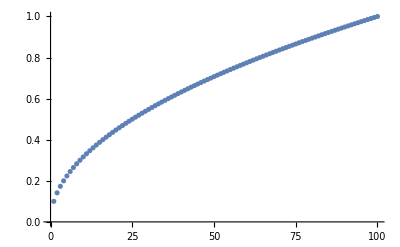

```mathematica
fac=100;
Table[{i,Sqrt[i/100]},{i,1,100}]//N
ListPlot[%]
```

```mathematica
Sqrt[1-z^2]/.z-> 2/(1-x^2)-1//PE
```

(2 ⅈ x)/((1-x) (1+x))